This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Accuracy Profiles of Annular Branches ch8AnnularAccuracyProfilies.nb

## Section 1: Choose test case

### testCase0001: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at the origin

```mathematica
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

Function: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

#### Expansion at infinity by prepending zero to singular points (testCase0001Inf0)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf0";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

### testCase0002: 15-degree with 1,2,3,4,5-cycle from paper 2, Function Genus: 86

#### Expansion at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
$theTestCase="testCase0002";
subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (z^30+1 z^32)+(z^14+1 z^20) w^5+(z^5+1 z^9) w^9+(z+1 z^3) w^12+(6) w^14+(2+1 z^2) w^15

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

$theTestCase="testCase0002Inf";
subDirectory=$theTestCase;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0003: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4 with removable singularity at origin

#### Expansion at zero

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003";


subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003Inf";
subDirectory=$theTestCase;

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;



If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
```

(z-1 z^2)+(3 z^2-4 z^3) w+(-9-1 z) w^2+(-4 z+4 z^2+8 z^3-2 z^4) w^3+(8+7 z-8 z^2+6 z^4) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0004: (22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9

#### Expansion at zero

```mathematica
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
$theTestCase="testCase0004";

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
subDirectory="testCase0004Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(2 z^2-5/2 z^3+2/5 z^7+22/3 z^8)+(1+7/4 z^2-1 z^5-137/12 z^8) w^3+(-14/5 z^7+13/20 z^8) w^4+(7/3 z^6+2 z^8) w^6+(-1/5 z^4-4 z^5+5/4 z^7-7/4 z^8) w^7+(-8/3 z^6+151/30 z^8) w^8+(-z^2+2 z^3-23/6 z^8) w^9

9

0

0

### testCase005: 19-degree expanded at s_2 with very small perimeter: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

```mathematica
$theFunction=(8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19;
$theTestCase="testCase0005";
aForm[$theFunction]//TeXForm

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

\left(\frac{8}{15}+\frac{29}{6} z-\frac{157}{15} z^2+\frac{37}{5} z^3\right)+\left(-4 z^2-\frac{29}{10} z^3\right)
   w^5+\left(-\frac{5}{3}-\frac{29}{5} z+\frac{3}{4} z^2-\frac{1}{2} z^3\right) w^6+\left(-\frac{11}{5}+\frac{7}{3}
   z+\frac{301}{30} z^3\right) w^{11}+\left(-1+\frac{40}{3} z^3\right) w^{19}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0005Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0006: (1-z^2)+w^2

#### Expansion at the origin

```mathematica
$theFunction=(1-z^2)+w^2
$theTestCase="testCase0006";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]//TeXForm
```

Function: (1-1 z^2)+(1) w^2

\left(1-1 z^2\right)+(1) w^2

### testCase0007: (z)+(1-4 z^2) w+(-1) w^2

#### Expansion at the origin

```mathematica
$theFunction=z+(1-4z^2)w-w^2
Print[Style[aForm[$theFunction],8]]
 subDirectory="testCase0007";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-w^2+z+w (1-4 z^2)

(z)+(1-4 z^2) w+(-1) w^2

(z)+(1-4 z^2) w+(-1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase007Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0008: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3
$theTestCase="testCase0008";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

9-7 w+w^3 (7 z-2 z^3)+w^2 (7-2 z-4 z^2-z^3)

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

3

0

-7

(9)+(-7) w+\left(7-2 z-4 z^2-1 z^3\right) w^2+\left(7 z-2 z^3\right) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0009: 9-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z)w^2+(3168+13/2 z)w^3+(-1230+4 z^5)w^4+(275/2+6z^2)w^5+(71-2 z^3)w^6-35 w^7+(20/3-2z)w^8+(-1/2-4 z)w^9

$theTestCase="testCase0009";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]]
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

486-35 w^7+w^9 (-1/2-4 z)+w^2 (-3591-3 z)+w^8 (20/3-2 z)-(8 z^4)/3-(33 z^6)/10+w^3 (3168+(13 z)/2)+w^5 (275/2+6 z^2)+w^6 (71-2 z^3)+w (1134-(2 z)/5-2 z^3)+w^4 (-1230+4 z^5)

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

9

0

1134

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase009Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0010: 14-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0010";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

14

0

-31/4

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];



subDirectory="testCase0010Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-589/60 z^9)+(-4/3 z-31/4 z^9) w+(-3/5+1/3 z^3-7 z^4+7 z^9) w^2+(7/4 z^5+17/12 z^8+119/20 z^9) w^3+(-8/3 z^5-1/5 z^6-119/20 z^9) w^7+(7/2+1 z^3-14 z^9) w^11+(-4 z^2+4 z^5+32/3 z^9) w^12+(4-12 z^5+85/12 z^9) w^13+(37/10 z^9) w^14

14

0

0

### testCase0016: Book example for Residue Theorem applied to annuli with non-zero sum of residues

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0016";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

\left(2+3 z-1 z^2\right)+\left(z^3+9 z^4\right) w+\left(-z-7 z^4\right) w^2+\left(2+4 z-4 z^3\right) w^4+\left(-8+1 z^2-7
   z^3+3 z^4\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

subDirectory="testCase0016Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(3-7 z+1 z^2-8 z^4) w^5

5

0

9

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3 (butterfly on cover of volume 1)

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
 subDirectory="testCase0017";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction]//TeXForm*)
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(1+2 z-3 z^15+8/3 z^22)+(11/3 z^6) w^5+(-5 z^5)w^12+(-8/3+z^3)w^14+(7/5+z^8)w^15+(3-z^3)w^20+(4-z^2)w^25+(-38/5-1/2 z)w^34

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

subDirectory="testCase0014Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

1+w^34 (-38/5-z/2)+2 z-5 w^12 z^5+(11 w^5 z^6)/3-3 z^15+(8 z^22)/3+w^25 (4-z^2)+w^20 (3-z^3)+w^14 (-8/3+z^3)+w^15 (7/5+z^8)

(8/3-3 z^7+2 z^21+1 z^22)+(11/3 z^16) w^5+(-5 z^17) w^12+(z^19-8/3 z^22) w^14+(z^14+7/5 z^22) w^15+(-z^19+3 z^22) w^20+(-z^20+4 z^22) w^25+(-1/2 z^21-38/5 z^22) w^34

34

0

0

### testCase0018: (z+1 z^2)+(1+1 z) w+(1) w^2

#### Expansion at the origin

```mathematica
$theFunction=(z+z^2)+(1+z)w+w^2

$theTestCase="testCase0018";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

w^2+z+z^2+w (1+z)

(z+1 z^2)+(1+1 z) w+(1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0018Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0019: (1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4 (polynomial solution at origin)

```mathematica
$theFunction=(1-3 z+3 z^2-z^3)+(-4+8 z-4 z^2)w+(6-6z)w^2-4 w^3+w^4;

$theTestCase="testCase0019";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print@Style[aForm[$theFunction],10]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

4

-3

-4

Origin is a singular point!

### testCase0020: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34 (Need 2000-digit working precision)

#### Expansion at zero

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0020";
aForm[$theFunction]//TeXForm
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

\left(-\frac{1043}{60}-\frac{5}{3} z^2+2 z^3-4 z^4-\frac{6}{5} z^5-\frac{2}{3} z^9+\frac{8}{3} z^{14}+\frac{25}{4} z^{15}+4
   z^{16}\right)+\left(\frac{11}{3}\right) w^5+\left(-\frac{8}{3}\right) w^{12}+\left(-\frac{38}{5}-\frac{1}{2} z\right)
   w^{34}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0020Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0021: (z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3 z^15-20 z^16) w^3+(3 z^7) w^4+(4 z^8) w^6+(3 z) w^8+(2) w^9+(5) w^10 (with three removable singular points at origin)

#### Expansion at the origin

```mathematica
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
$theTestCase="testCase0021";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

-z^2+z^3+w (-4 z+3 z^2)+w^3 (-2+8 z+4 z^2-4 z^3)+w^2 (-z^3-9 z^4)+w^4 (6-8 z^2+7 z^3+8 z^4)

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0021Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

(3 z+1 z^2)+(5+2 z^6) w^2+(-20+3 z) w^3+(3 z^9) w^4+(4 z^8) w^6+(3 z^15) w^8+(2 z^16) w^9+(5 z^16) w^10

10

3

0

### testCase0022: 50-degree function

```mathematica
$theFunction=$theFunction=2 z^6+z^7/2-(5 z^11)/4+4 z^22+(29 z^34)/10-z^40-(13 z^43)/2+w^38 (z^2-z^7/4)+w^49 (-z^9+z^13/4+2 z^14)+w^34 ((7 z^14)/3-(3 z^18)/2)+w^47 (z^10/3+(7 z^11)/4+(8 z^21)/5)+w^24 (4 z^8+(4 z^25)/5-(3 z^27)/2)+w^9 (-(6 z^2)/5-z^6/2+(7 z^31)/3)+w^16 ((7 z^21)/3+(4 z^27)/5+(4 z^32)/3)+w^18 (-6 z^14-2 z^31-z^33)+w^3 (2 z^17+(7 z^34)/2)+w^16 (-(3 z^5)/4-2 z^36+z^39/3)+w^50 (-z^23/3-(7 z^40)/2+z^42)+w^4 (-(3 z^30)/2+(4 z^38)/3+(8 z^42)/5)+w^33 (-3 z^4+(8 z^22)/3-(8 z^43)/5)+w^16 (-z^26/4-(3 z^41)/4-z^43)+w^48 ((2 z^2)/3+6 z^26+(3 z^43)/5)+w^49 (2 z^18+z^36-2 z^44)+w^10 (-(2 z^11)/5-(3 z^26)/2+z^45)+w^40 (-z^20/2-z^29+z^46)+w^36 (-4+8 z^13-(7 z^47)/4)+w^14 ((7 z^24)/5-6 z^32-6 z^49)+w^22 (-2 z^27-(8 z^50)/3)+w^2 ((3 z^10)/5+(7 z^24)/4-z^50/4);
$theTestCase="testCase0022";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];



Print[Style[aForm[$theFunction],8]]
```

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Function: (2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Origin is a singular point!

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0022Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0023: 12-degree funtion with three 4-cycle branches at origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 


$theTestCase="testCase0023";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


Print[Style[aForm[$theFunction],8]]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Function: (-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Origin is a singular point!

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0023Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z)+(1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^2+(721/20736+(55 ⅈ)/216-28398241/71663616 z) w^4+(-293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(28398241/71663616+5329/20736 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336) w^12

12

-20475131761/8916100448256-(1561903255 ⅈ)/92876046336

0

\left(-\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}
   z\right)+\left(\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272} z\right) w^2+\left(\frac{721}{20736}+\frac{55
   i}{216}-\frac{28398241}{71663616} z\right) w^4+\left(-\frac{293095}{746496}-\frac{5329 i}{15552}+\frac{389017}{746496}
   z\right) w^6+\left(\frac{28398241}{71663616}+\frac{5329}{20736} z\right)
   w^8+\left(-\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272}\right)
   w^{10}+\left(\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}\right) w^{12}

### testCase0024: 5-degree function with multiple polygons

#### Expansion at zero

```mathematica
$theFunction=(z^4)+(2 z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

$theTestCase="testCase0024";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

Print[Style[aForm[$theFunction],8]]
aForm[$theFunction]//TeXForm
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Function: (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Origin is a singular point!

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

\left(z^4\right)+\left(2 z^2+1 z^4\right) w+\left(1+1 z^2+1 z^3\right) w^2+(z) w^3+\left(\frac{1}{4}-\frac{1}{2} z\right)
   w^4+\left(-\frac{1}{2}\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0024Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0025: z-∑_(j=1)^n (w-j)^j (each value of n is a separate subdirectory)

#### Expansion at the origin

```mathematica
iterationMax=7;
$theFunction=z-Product[(w-j)^j,{j,1,iterationMax}];

subDirectory="testCase0025"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

NSolve[$theFunction==0/.z->0,w]
```

Function: (-3319766398771200000+1 z)+(23238364791398400000) w+(-77030436760058880000) w^2+(161326036746072576000) w^3+(-240180965385332025600) w^4+(271057611231886800384) w^5+(-241386405085113410304) w^6+(174299255833816957824) w^7+(-104039758639368727776) w^8+(52067305426360848992) w^9+(-22077583830099907600) w^10+(7993549830308360568) w^11+(-2485349318616140689) w^12+(666179931589106948) w^13+(-154307800127905488) w^14+(30917671615556572) w^15+(-5356632994052156) w^16+(801097015860804) w^17+(-103080193140016) w^18+(11355388042796) w^19+(-1063406184918) w^20+(83839010860) w^21+(-5491243184) w^22+(293354100) w^23+(-12452860) w^24+(404012) w^25+(-9408) w^26+(140) w^27+(-1) w^28

{{w→1.},{w→2.},{w→2.},{w→3.},{w→3.},{w→3.},{w→4.},{w→4.},{w→4.},{w→4.},{w→5.},{w→5.},{w→5.},{w→5.},{w→5.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.}}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
iterationMax=5;
tempFunction=z-Product[(w-j)^j,{j,1,iterationMax}];
aForm[tempFunction]

subDirectory="testCase0025Inf"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[tempFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(tempFunction/.z->1/z)];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

(86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

(1+86400000 z)+(-432000000 z) w+(981360000 z) w^2+(-1348952000 z) w^3+(1258456700 z) w^4+(-845928448 z) w^5+(424015067 z) w^6+(-161614309 z) w^7+(47283632 z) w^8+(-10629552 z) w^9+(1822678 z) w^10+(-234290 z) w^11+(21868 z) w^12+(-1400 z) w^13+(55 z) w^14+(-z) w^15

15

### testCase0027: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0027";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

 

Print[Style[aForm[$theFunction],8]]
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0027Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0028: test case for use in constructing fully-ramified branch at infinity

#### Expansion at the origin

```mathematica
$theFunction=theReformedF;
$theTestCase="testCase0028";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
Style[aForm[$theFunction],10]
```

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

34

0

0

Origin is a singular point!

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=theReformedF;
$theTestCase="testCase0028Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
Print["recomInfinityF: ",Style[aForm[recomInfinityF],10]];
Print["$theFunction:    ",Style[aForm[$theFunction],10]]
```

(-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

34

0

0

recomInfinityF: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

theFunction:    (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

### testCase0031: -17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

Note this problem produces a Groebner basis function with 12 singular points, three of which are poles and the remaining are removable.

#### Expansion at the origin

```mathematica
baseFun=(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+1/4 z^2)w;
Print@Style[baseFun,10]
gb1=GroebnerBasis[baseFun,z];
$theFunction=gb1[[1]];
aForm[$theFunction]


$theTestCase="testCase0031"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

(*fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
*)
```

-17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

testCase0031

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

4

-21307392

0

### TestCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
$theTestCase="testCase0032"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

testCase0032

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

Origin is a singular point!

### testCase0033: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(z(z-3)(z+3))w^3;

$theTestCase="testCase0033"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
aForm[$theFunction]
```

testCase0033

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

3

0

-7

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0033Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0034: ((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2)) Function is reducible!

#### Expansion at the origin (aForm does not work with imaginary I in expression !)

```mathematica
f1[z_]:=((1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z))/((z^2+(4+4 ⅈ))^(3/2));
gb=GroebnerBasis[(1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z)-(z^2+(4+4 ⅈ))^(3/2)w==0,{z,w}];

factorGB= Factor[gb[[1]]]
$theFunction=factorGB[[1]]

subDirectory="testCase0034";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction] aForm does now work for this function ! *)
Print[f1[z]]
```

((16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6) ((16+16 ⅈ)+128 ⅈ w-(128-128 ⅈ) w^2+(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2+36 w z^4+(12+12 ⅈ) w^2 z^4+(2-2 ⅈ) w z^6+w^2 z^6)

(16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6

2

0

-128 ⅈ

Origin is a singular point!

((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2))

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0035: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^7)w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7 z^3+3 z^4)w^5
$theTestCase="testCase0035"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)+w^2 (-z-7 z^7)

testCase0035

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

### testCase0036 (function with multiple polygons): (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

#### Expansion at the origin

```mathematica
$theFunction=z^4+(2z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

 subDirectory="testCase0036";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

5

0

0

Origin is a singular point!

### testCase0037: 33-degree function with 1762 finite singular points, Genus =885

#### Expansion at the origin

```mathematica
(* genus 885  with 1762 singular points *)
 
$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;
polyForm[$theFunction,w]
$theTestCase="testCase0037";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

fz=D[$theFunction,z]/.{z->0,w->0};
fw=D[$theFunction,w]/.{z->0,w->0};
If[fz==0 && fw==0,
Print[Style["Function has indeterminate form at origin!",Red,Bold]];
];
```

#### Expansion at infinity (no single-cycles at infinity)

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;


cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList)
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0037Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

34

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^32) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^26) w^29+(5 z^7+2 z^33) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

33

### testCase0038: (-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

#### Expansion relative to the origin

```mathematica
$theFunction=(-1/2+z)+(3/2+z^2)w+(-7/4+2 z)w^2+(5/4+z^3)w^3+(-1/12+2 z)w^4+(1/4+z^3)w^5+(-4+z)w^6+(16/3+z)w^7+(-2+z)w^8;
functionSave=$theFunction;

$theTestCase="testCase0038";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

Print[Style[aForm[$theFunction],8]]
```

(-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

### testCase0039: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

(z-1 z^2)+(-1) w^2

2

1

0

#### Expansion at infinity

```mathematica
$theFunction=z(1-z)-w^2
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0039Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-w^2+(1-z) z

(-1+1 z)+(-z^2) w^2

2

### testCase0040: Beta z^(1/3)(1-z)^(1/2)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0040";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

6

z^2-3 z^3+3 z^4-z^5

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

0

0

### testCase0041: Beta z^(1/3)(1-z)^(1/4)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=4;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

12

z^4-3 z^5+3 z^6-z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

12

0

0

### testCase0043: Beta z^(5/3)(1-z)^(5/7)

```mathematica
theP=5;
theQ=3;
theR=5;
theS=7;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0043";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

21

z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-z^50

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

0

0

### testCase0045: 25-degree function with NSolve char roots precision of sing 714 returns zero precision. Need to increase working precision of singular points to 2500 to resolve problem

#### Expansion at origin

```mathematica
(*
 function with 6-cycle at sp 17,18,52 with sp 17 having 1-cycle extending to furthest sp 72 distance of 1530
*)
$theTestCase="testCase0045";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)
polyForm[$theFunction,w]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)

++(-407/12+2 z^7+(8 z^9)/5)(-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)w^2(811/30+4 z+(4 z^7)/3-2 z^14)w^4(-19/12)w^7(167/20-(17 z)/4+(8 z^13)/5)w^8(99/20+(7 z^11)/3)w^9(-821/60+7 z^17)w^12(13/3)w^14(-29/15-2 z^9-z^13)w^15(-569/60-z^3-2 z^18)w^16(-379/30-2 z)w^17(41/3-(5 z^3)/2)w^18(-107/12)w^19(5/2-(3 z^13)/5)w^25

25

### testCase0046: 4-degree function with removable singularity in path of NDSolve CLSP calculation

```mathematica
$theTestCase="testCase0046";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

{0.,0.,0.}

### testCase0047: 1-(3+4 z+4 z^2)w^2

```mathematica
$theTestCase="testCase0047";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=1-(3+4 z+4 z^2)w^2;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+4 z+4 z^2)+(-1) w^2

2

4

0

### testCase0048: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

#### Expansion at the origin

```mathematica
$theTestCase="testCase0048";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 $theFunction=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;




Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

7

61/20

37/4

\left(-\frac{301}{15}+\frac{61}{20} z+\frac{44}{5} z^2-\frac{67}{6} z^3+\frac{133}{20}
   z^4\right)+\left(\frac{37}{4}+\frac{1}{2} z^2+\frac{7}{2} z^3\right) w+\left(\frac{47}{5}+1 z^2+3 z^4\right)
   w^2+\left(-\frac{189}{20}-\frac{3}{2} z^3\right) w^4+\left(-\frac{23}{10}-\frac{7}{2} z^2\right)
   w^5+\left(-\frac{779}{60}+\frac{3}{4} z+4 z^2+3 z^3-\frac{1}{3} z^4\right) w^6+\left(-\frac{17}{2}+1 z^2-\frac{3}{4}
   z^{12}\right) w^7

### testCase0050: use fractional expression to generate ramify pole with residue

```mathematica
$theTestCase="testCase0050";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

{{w→-3.88933},{w→-2.},{w→0.194664-0.690169 ⅈ},{w→0.194664+0.690169 ⅈ}}

4

5

0

\left(3+5 z-8 z^2+8 z^3\right)+\left(4 z+8 z^2+1 z^4-1 z^5\right) w^2+\left(z^3+10 z^4\right) w^3+\left(2 z^4\right) w^4

{0.,0.,0.}

### testCase0055: example of residual ramified pole at origin

#### Expansion at zero

```mathematica
$theTestCase="testCase0055";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
```

Function: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

#### Expansion at infinity

```mathematica
theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
$theTestCase="testCase0051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];
$theFunction=newFunction;




aForm[$theFunction]
```

(-z^2+2 z^4)+(3 z^2-4 z^4) w+(-9-1 z) w^2+(8 z^3-2 z^4) w^3+(-8 z^2+1 z^3) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0060: 15-degree function

#### Expansion at zero

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15;

$theTestCase="testCase0060";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10) w^3+(-179/12+1 z-10/3 z^2+4/3 z^3+7/2 z^14) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12) w^10+(1/2 z^4) w^11+(-10/3-1 z) w^15

#### Expansion at infinity

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15
$theTestCase="testCase0060Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
functionDegree=Last@wExp;

aForm[$theFunction]
```

2+w^15 (-10/3-z)-(5 z^3)/2+(w^11 z^4)/2+z^5/5+w^7 (26/5-z^3)+w^3 ((2 z)/3+4 z^3+z^10/4)+w^10 (205/12+z^3/2-6 z^7+(4 z^12)/3)+w^5 (-179/12+z-(10 z^2)/3+(4 z^3)/3+(7 z^14)/2)

(1/5 z^9-5/2 z^11+2 z^14)+(1/4 z^4+4 z^11+2/3 z^13) w^3+(7/2+4/3 z^11-10/3 z^12+1 z^13-179/12 z^14) w^5+(-z^11+26/5 z^14) w^7+(4/3 z^2-6 z^7+1/2 z^11+205/12 z^14) w^10+(1/2 z^10) w^11+(-z^13-10/3 z^14) w^15

```mathematica
(* end of section *)
```

61.9333

### testCase0061: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5 (set up only one pole at infinity)

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5
$theTestCase="testCase0061"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

2-8 w^5+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w (z^3+9 z^4)

testCase0061

Function: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5;
$theTestCase="testCase0061Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(-8 z^4) w^5

5

3

0

### testCase0062: 5-degree function

#### Expansion at the origin

```mathematica
$theFunction=(-4+1/3 z^3)+(15/4-3 z^4+8 z^5)w^3+(-22/3)w^5
$theTestCase="testCase0062"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-4-(22 w^5)/3+z^3/3+w^3 (15/4-3 z^4+8 z^5)

testCase0062

Function: (-4+1/3 z^3)+(15/4-3 z^4+8 z^5) w^3+(-22/3) w^5

### testCase0064: 24-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/2+2 z^2)+ (-4z^2)w^4+ (-4 z^4)w^6+ (2-z^6)w^7+ (11/5 z^10)w^9+ (8 z^7)w^12+ (8 z^97)w^13+ (-8/3 z)w^15+  (1/2z^4)w^16+ (5/2 z^6)w^18+ (z^3)w^20+ (11/4 z^3)w^21+ (-5/7 z^7)w^22+ (-5 z^7)w^23+(4+1/4 z^5)w^24;
$theTestCase="testCase0064"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

testCase0064

Function: (1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

Function: (1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

### testCase0065: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=((z-1/2)(2-z+2 z^4))+((z-1/2)(3+2 z^2)) w+((z-1/2)(1/2-1/4 z^4+1/2 z^7)) w^2+(z-1/2)(1/2+2 z^4+1/2 z^7)w^6+(z-1/2)(2-z^6)w^7+(z-1/2) w^9+(z-1/2)(8 z^7) w^12+(z-1/2)w^14+(-8/3)w^15;

$theTestCase="testCase0065";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

(-1+5/2 z-1 z^2-1 z^4+2 z^5)+(-3/2+3 z-1 z^2+2 z^3) w+(-1/4+1/2 z+1/8 z^4-1/4 z^5-1/4 z^7+1/2 z^8) w^2+(-1/4+1/2 z-1 z^4+2 z^5-1/4 z^7+1/2 z^8) w^6+(-1+2 z+1/2 z^6-1 z^7) w^7+(-1/2+1 z) w^9+(-4 z^7+8 z^8) w^12+(-1/2+1 z) w^14+(-8/3) w^15

### testCase0066: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(z-1)+(47/20+5/2 z^2+29/15 z^4+z^6)w^5+(-3/4+4/3 z^2-3/2 z^3) w^7+(-19/12+2 z^2+19/15 z^3)w^10+(9/2-8 z^5)w^11+(-39/20+2/5 z^3)w^13+(2+z^3-3z^5)w^15;

$theFunction=-(z-1)^3-4(z-1)^2w-6(z-1)w^2-4 w^3+w^4;

$theTestCase="testCase0066";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
```

Origin is a singular point!

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

{0.,0.,0.,4.}

0

0

### testCase0067: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2)w^3+(-179/12+z)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3)w^10+(-10/3-z)w^15
$theTestCase="testCase0067";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+(w^14 z^4)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (-10/3-z) (205/12+z^3/2)

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (205/12+z^3/2)

(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2) w^3+(-179/12+1 z) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3) w^10+(-10/3-1 z) w^15

{-1.00482-0.781012 ⅈ,-1.00482+0.781012 ⅈ,-0.819871-0.529671 ⅈ,-0.819871+0.529671 ⅈ,-0.507586,-0.147915-0.40623 ⅈ,-0.147915+0.40623 ⅈ,0.296776-1.16658 ⅈ,0.296776+1.16658 ⅈ,0.40112-0.255737 ⅈ,0.40112+0.255737 ⅈ,0.422918-1.0185 ⅈ,0.422918+1.0185 ⅈ,0.91459,1.29659}

-13/2

0

\left(2-\frac{5}{2} z^3+\frac{1}{5} z^5\right)+\left(\frac{1}{2}+\frac{2}{3} z^2\right) w^3+\left(-\frac{179}{12}+1 z\right)
   w^5+\left(\frac{26}{5}-1 z^3\right) w^7+\left(\frac{205}{12}+\frac{1}{2} z^3\right) w^{10}+\left(-\frac{10}{3}-1 z\right)
   w^{15}

### testCase0068: 33-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/3 z^24+2/5 z^31)+(3/4 z^34)w^4+(-1/5 z^21-3/2 z^29+2/3 z^33)w^5+(-1/2 z^32)w^7+(-z^26)w^8+(-1/5 z^4)w^9+(3/2 z^22)w^11+(-z-z^3)w^13+7 z^20 w^14+2 z^7 w^15+(6/5 z^12) w^17+(-7/3 z^12)w^21+2 z^18 w^23+2 z^31 w^25+2 w^28+2 z^36 w^29+(5 z^7 2 z^33)w^30+(1/5 z^16) w^31+(1/3 z^16)w^33;
$theTestCase="testCase0068";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

Origin is a singular point!

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^22) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^36) w^29+(10 z^40) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

{-2.99412,-0.96735-0.149106 ⅈ,-0.96735+0.149106 ⅈ,-0.864141-0.261474 ⅈ,-0.864141+0.261474 ⅈ,-0.814218-0.535666 ⅈ,-0.814218+0.535666 ⅈ,-0.587098-0.481202 ⅈ,-0.587098+0.481202 ⅈ,-0.576816-0.853386 ⅈ,-0.576816+0.853386 ⅈ,-0.389138-0.769409 ⅈ,-0.389138+0.769409 ⅈ,-0.23213-0.976286 ⅈ,-0.23213+0.976286 ⅈ,0.0652535-0.840687 ⅈ,0.0652535+0.840687 ⅈ,0.138462-0.997922 ⅈ,0.138462+0.997922 ⅈ,0.43243-0.808062 ⅈ,0.43243+0.808062 ⅈ,0.470129-0.719257 ⅈ,0.470129+0.719257 ⅈ,0.646012-0.574844 ⅈ,0.646012+0.574844 ⅈ,0.814297-0.566424 ⅈ,0.814297+0.566424 ⅈ,0.839-0.140043 ⅈ,0.839+0.140043 ⅈ,0.926413-0.223338 ⅈ,0.926413+0.223338 ⅈ,1.59596-2.73047 ⅈ,1.59596+2.73047 ⅈ}

102/5

0

\left(\frac{1}{3} z^{24}+\frac{2}{5} z^{31}\right)+\left(\frac{3}{4} z^{34}\right) w^4+\left(-\frac{1}{5} z^{21}-\frac{3}{2}
   z^{29}+\frac{2}{3} z^{33}\right) w^5+\left(-\frac{1}{2} z^{32}\right) w^7+\left(-z^{26}\right) w^8+\left(-\frac{1}{5}
   z^4\right) w^9+\left(\frac{3}{2} z^{22}\right) w^{11}+\left(-z-1 z^3\right) w^{13}+\left(7 z^{20}\right) w^{14}+\left(2
   z^7\right) w^{15}+\left(\frac{6}{5} z^{12}\right) w^{17}+\left(-\frac{7}{3} z^{12}\right) w^{21}+\left(2 z^{18}\right)
   w^{23}+\left(2 z^{31}\right) w^{25}+(2) w^{28}+\left(2 z^{36}\right) w^{29}+\left(10 z^{40}\right) w^{30}+\left(\frac{1}{5}
   z^{16}\right) w^{31}+\left(\frac{1}{3} z^{16}\right) w^{33}

### testCase0069: Beta function z^(3/5)(1-z)^(2/5)

```mathematica
subDirectory="testCase0069";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=3;
theQ=5;
theR=2;
theS=5;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### testCase0093:

```mathematica
$theFunction=(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+z^2-z^3)w^6+(-1/2+2 z^5)w^7+(1/2 z^4+4/3 z^5)w^8+(-5/3+z^2)w^10+(-3 z^3)w^11+(1+2 z^4+3 z^5)w^15

$theTestCase="testCase0093";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### Temp test case

```mathematica
randomPolynomial[z_,n_,coeffRange_:{-10,10}]:=RandomInteger[coeffRange,n+1].Table[z^i,{i,0,n}]

$theFunction=(z-1)^4 randomPolynomial[z,6,{-5,5}]-w^9
$theFunction=w^2-z^3;
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]


$theTestCase="tempTestCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

-w^9+(-1+z)^4 (1-2 z-z^3-4 z^4+z^5-5 z^6)

(-z^3)+(1) w^2

Function: (-z^3)+(1) w^2

Origin is a singular point!

(-z^3)+(1) w^2

### Generate random polynomial with real coefficients

```mathematica
randomType=1;
wExpMax=4
If[randomType==1,
sparseVal=2;

$theFunction=getRandomRealPoly[wExpMax,sparseVal];
,
zExpMax=18;
zPolySize=12;

sparseVal=2;$theFunction=getRandomPoly[zExpMax,zPolySize,wExpMax,sparseVal];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]
```

4

(21/5+2 z^3+1 z^5)+(-257/30) w+(-71/15+2 z^3+2 z^4) w^2+(6) w^3+(-25/6-33/10 z) w^4

## Section 2: Create Annular Template and import data from Ch. 7 notebook

### Section 2.1: Create Annular Template and compute singular data

```mathematica
(*
 create annular table 
*)

 implicitF[z_,w_]=$theFunction;
 {$theSingularList,argList,$zeroIndexes,$poleIndexes,$minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,singTableAnnulusIndexes,singTableSingIndexes,plottingRadiiTable,annulusTableTemplate,annulusTableRTemplate}=getAnnularTemplate[$theFunction];
annulusTableReport=Prepend[annulusTableRTemplate,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
(*Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];
*)
```

poleIndexes: {1,8}

Routine for singular point at zero

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 |   |   |   |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   |   |   | {} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 |   |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 |   |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   |   |   | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 |   |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 |   |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   |   |   | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 |   |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 |   |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   |   |   | {} |   |  
  | 8 | 1.33333 | 0.205603 | 0. |   |   | {} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   |   |   | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 |   |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 |   |   | {} |   |  
6 |   | {1.7028,5.7028} | 3.7028 |   |   |   | {} |   |

### Section 2.2: Import Annular Table with continuations

```mathematica
If[FileExistsQ[annularTableWithContinuationsFileName[$theTestCase]],
  {annulusTable,annulusTableR}=Import[annularTableWithContinuationsFileName[$theTestCase]];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
Print[Style[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}],10]];
,
Print[Style["Annular table with continuations not found.  See Ch. 7 notebook.",Red]];
]
```

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 | 0.166667 |   | {{1},{2},{3}} |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   | {{1},{2},{3}} | {{1},{2},{3}} | {{{1},{1}}} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 | {{2,3},{1}} |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 | {{2,3},{1}} |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   | {{1},{2},{3}} | {} | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 | {{2,3},{1}} |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 | {{2,3},{1}} |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   | {{1,3,2}} | {} | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 | {{1,2},{3}} |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 | {{1,2},{3}} |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   | {{1,3,2}} | {{1,3,2}} | {{{1,3,2},{1,3,2}}} |   |  
  | 8 | 1.33333 | 0.205603 | 0. | {{1},{2},{3}} |   | {{1,3,1}} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   | {{1,3,2}} | {} | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 | {{2,3},{1}} |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 | {{1,3},{2}} |   | {} |   |  
6 |   | {1.7028,2.7028} | 2.2028 |   | {{1},{2},{3}} |   | {} |   |

### Section 2.3: Import graphics annular table with branch links

Importing D:\algFunctionBook\data\testCase0017\annularTableWithBranchLinks.m

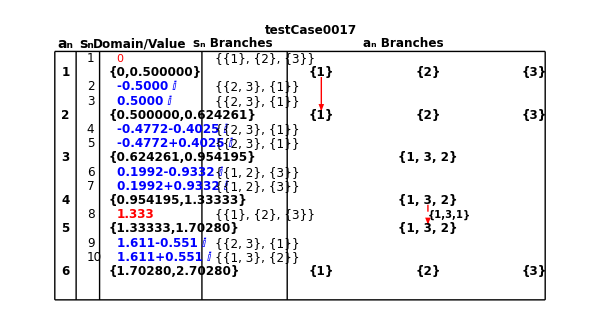

```mathematica
implicitF[z_,w_]=$theFunction;
If[FileExistsQ[annularTableWithBranchLinksFileName[$theTestCase]],
Print["Importing ",annularTableWithBranchLinksFileName[$theTestCase]]; 
 annularTableWithLinks=Import[annularTableWithBranchLinksFileName[$theTestCase]];
(* adjust size as necessary *)
Show[annularTableWithLinks,ImageSize->600]
,
Print[Style[annularTableWithBranchLinksFileName[$theTestCase]<>" not found during import",Red]];
]
```

### Section 2.4 Import final continuation data

```mathematica
If[FileExistsQ[finalContinuationDataFileName[$theTestCase]],

 {theFinalContinuationList,theRingDomainIndex}=Import[finalContinuationDataFileName[$theTestCase]];
(*theFinalContinuationList//N//MatrixForm
*)

annularExtensions={#[[1]],#[[2,All,{1,3}]]}&/@ theFinalContinuationList;
Print[Row[{Grid[Prepend[annularExtensions,{"a_n","{{Branch,{r_a,r_b}}"}],Dividers->{{{True}},{True,True,{False},True}},Alignment->Left],Spacer[15],Grid[Prepend[theRingDomainIndex//N,{"Ring index","Value"}],Dividers->{{{True}},{True,True,{False},True}}]}]];
,
Print[Style[finalContinuationDataFileName[$theTestCase]<>" not found during import.",Red]];
];
```

a_n | {{Branch,{r_a,r_b}}
1 | {{{1},{1,3}},{{2},{1,2}},{{3},{1,2}}}
2 | {{{2},{2,3}},{{3},{2,3}}}
3 | {{{1,3,2},{3,4}}}
4 | {{{1,3,2},{4,5}}}
5 | {{{1,3,2},{5,6}}}
6 | {{{1},{6,7}},{{2},{6,7}},{{3},{6,7}}}Ring index | Value
1. | 0.
2. | 0.5
3. | 0.624261
4. | 0.954195
5. | 1.33333
6. | 1.7028
7. | ∞

### Section 2.5: Import Extended Branch Summary

```mathematica
If[FileExistsQ[finalBranchGridReportFileName[$theTestCase]],
finalBranchGrid=Import[finalBranchGridReportFileName[$theTestCase]];
Print[finalBranchGrid];
,
Print[Style[finalBranchGridReportFileName[$theTestCase]<>" not found during import.",Red]];
];
```

a_i | Branch Domains
1 | {{1}
{s_1,s_4},{2}
{s_1,s_2},{3}
{s_1,s_2}}
2 | {{2}
{s_2,s_4},{3}
{s_2,s_4}}
3 | {{1,3,2}
{s_4,s_6}}
4 | {{1,3,2}
{s_6,s_8}}
5 | {{1,3,2}
{s_8,s_9}}
6 | {{1}
{s_9,s_∞},{2}
{s_9,s_∞},{3}
{s_9,s_∞}}

## Section 3: Select branch in branch summary table and generate an extended differential branch plot

### Section 3.1: Set up User Menu

```mathematica
extendedAnnularBranchPlotMenu=Labeled[Column[{Row[{Style["AnnulusIndex:",Black,Bold],Spacer[5],InputField[Dynamic@$selectedAnnulus,FieldSize->2],Spacer[12],Style["Branch index:",Black,Bold],Spacer[5],InputField[Dynamic@$selectedMonodromyIndex,FieldSize->2]}],
Row[{Style["Plot type: ",Black,Bold],RadioButtonBar[Dynamic[$plotType],{Re,Im}]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}]
},Frame->True,FrameStyle->Thick],Style["Extended annular branch plot menu",Bold,Black],Top]
```

AnnulusIndex:Branch index:
Plot type:  | Re   | Im
Show plot label Extended annular branch plot menu

### Section 3.2: Create differential plot

```mathematica
(* select annular domain and branch position in finalBranchGrid *)
selectedAnnulus=$selectedAnnulus
selectedBranch=$selectedMonodromyIndex


annularExtensions={#[[1]],#[[2,All,{1,2,3}]]}&/@ theFinalContinuationList;
theAnnulusTable=annulusTable;

If[selectedAnnulus>Length@annularExtensions || selectedBranch>Length@annularExtensions[[selectedAnnulus,2]],
Print[Style["Selected branch or annulus out of range",Red]];
,
{theBranchMonodromy,extendedDomain,theBranchSet}=getExtendedBranchPlot[theAnnulusTable,$plotType,selectedAnnulus,selectedBranch,$thetaV,annularExtensions,"radialSegments"->25,"arcSegments"->50];

 branchPlot=Table[
rowA=theBranchSet[[k]]//N;
rowB=theBranchSet[[k+1]]//N;
pTable=Table[{Blue,Opacity[0.25],Polygon[{rowA[[j]],rowA[[j+1]],rowB[[j+1]],rowB[[j]]}]},{j,1,(Length@rowA)-1}];pTable,
{k,1,(Length@theBranchSet)-1}
];
theDifferentialPlot= Show[Graphics3D@{branchPlot},BoxRatios->{1,1,2},Axes->True,AxesLabel->{Style["Re(z)",14,Bold,Black],Style["Im(z)",14,Bold,Black],Style[ ToString[$plotType]<>"(w)",14,Black,Bold]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{0,0,-1}},FaceGridsStyle->Directive[Black,Bold],ImageSize->300(*PlotRange->{Automatic,Automatic,{-1,5}}*)];

thePlotRange=PlotRange[theDifferentialPlot];
Print[theDifferentialPlot];
];

theAnnulus=extendedDomain;
$theAnnulus=extendedDomain;
theCurrentBranchSize=Length@theBranchMonodromy
$selectedBranchSize=theCurrentBranchSize
```

4

1

This branch is not analytically extended

-Graphics3D-

3

3

## Section 4: Import precise analytic and singular expansions for inner annular domains, a_2 through a_{n-1}.

This section is used to generate accuracy profiles for inner annular domains (not a_1 or a_{n}) as these can be generated by the Chatper 5 notebook (the a_n domain profiles are determined by the a_1 expansion at infinity).

### Section 4.1: Import combinedExpansion terms previously generated by the chapter 6 notebook

Note:  The annular power expansions for the base annular branch must be available for import.  For example if the {1,2} branch in a_ 4 extends into a_ 25, then the power expansions for the a_ 4 (1,2) branch must be available for import to generate the extended branch with domain a_4 through a_25  with its power expansions.

```mathematica
If[$selectedAnnulus==Length@theAnnuli|| $selectedAnnulus==1,
Print[Style["This section is for inner annular domains 2 through n-1 with n the total annuli",Red]];
Print[Style["Accuracy studies of a_1 are done with the chapter 5 notebook",Red]];
,
If[FileExistsQ[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,theBranchMonodromy]],
Print["Importing ",combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,theBranchMonodromy]];
 {analyticTerms,analyticOrderList,singularTerms,singularOrderList} =Import[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,theBranchMonodromy]];
maxAnalyticOrder=analyticOrderList[[-1,1]];
maxSingularOrder=singularOrderList[[-1,1]];
maxSeriesOrder=Min[maxAnalyticOrder,maxSingularOrder];
Print["maxSeriesOrder: ",maxSeriesOrder];
Print["Size of analytic Terms: ",Length@analyticTerms," prec: ",Precision@analyticTerms];
Print["Size of singular terms: ",Length@singularTerms," prec: ",Precision@singularTerms];
Print["The extendedDomain: ",extendedDomain//N];
,
Print[Style["Combined annular expansion file "<>combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,theBranchMonodromy]<>" not found.  Create this file with the chapter 6 notebook",Red]];
];
];
```

Importing D:\algFunctionBook\data\testCase0017\a4b132combinedExpansionTerms.m

maxSeriesOrder: 99

Size of analytic Terms: 301 prec: 145.404

Size of singular terms: 201 prec: 139.199

The extendedDomain: {0.954195,1.33333}

## Section 5: Accuracy analysis of inner annular domains

### Section 5.1: Create radius ratios and seriesArray of normal series indexed by order

```mathematica
$theAnnulus//N

thetaRange=Array[#&,100,{-Pi,Pi}];
(* if outer annulus, can try larger domains *)
radiusRange=Array[#&,80,$theAnnulus];
radiusRatios=Array[#&,100,{1/100,99/100}];
radiusStart=$theAnnulus[[1]];
radiusDif=radiusRange[[-1]]-radiusRange[[1]];
finalReducedSeries[z_]=(Plus@@analyticTerms)+(Plus@@singularTerms);
Print["Max order: ",maxSeriesOrder];

seriesTable=Table[(Plus@@analyticTerms[[1;;analyticOrderList[[orderIndex,2]]]])+(Plus@@singularTerms[[1;;singularOrderList[[orderIndex,2]]]]),
{orderIndex,1,maxSeriesOrder}
];

 theexp=Exponent[finalReducedSeries[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[finalReducedSeries[z],z,theexp];
branchSheetF[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/$selectedBranchSize])^($selectedBranchSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];
```

{0.954195,1.33333}

Max order: 99

### Section 5.2: Generate accuracy plot at constant theta and radius ratio as a function of order

the radius ratio: 2353/9900

theRadius: 1.04431

zVal: 1.04431

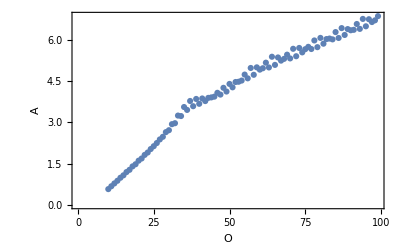

```mathematica
plotColors={Red,Blue,Yellow,Green,Orange,Purple,Pink};
theTheta=SetPrecision[thetaRange[[35]],1000];
rIndex=24;
Print["the radius ratio: ",radiusRatios[[rIndex]]];
theTheta=SetPrecision[Pi/4,1000];
theRadius=SetPrecision[radiusRange[[1]]+(radiusRatios[[rIndex]]radiusDif),1000];
Print["theRadius: ",theRadius//N];
zVal=theRadius Exp[I theTheta];
Print["zVal: ",Abs@zVal//N]

 theOrderErrorTable=Table[

(*pVal=(Plus@@reducedAnalyticTerms[[1;;analyticOrderIndexList[[oIndex,2]]]])+(Plus@@theReformedSingularTerms[[1;;singularOrderIndexList[[oIndex,2]]]])/.z->zVal;*)
pVal=seriesTable[[oIndex]]/.z->zVal;
wVals=w/.NSolve[$theFunction==0/.z->zVal,WorkingPrecision->65];
errTable=Abs[#-pVal]&/@ wVals;

pos=Position[errTable,Min[errTable]][[1,1]];

(*{radiusRatios[[n]],errTable[[pos]]//N,-MantissaExponent[errTable[[pos]]][[2]]},*)
{oIndex,errTable[[pos]]//N,-Log[10,errTable[[pos]]]},
{oIndex,10,maxSeriesOrder}
];

ListPlot[theOrderErrorTable[[All,{1,3}]],Frame->True,FrameLabel->{Style["O",16,Black,Bold],Rotate[Style["A",16,Black,Bold],-90 Degree]}]
```

### Section 5.3: Generate accuracy vs. radius at selected order and find max accuracy radius ratio

maxRadiusRatio: 0.336667

Ratio index: 34

Maximum accuracy radius: 1.08184

Maximum accuracy: 7.66314

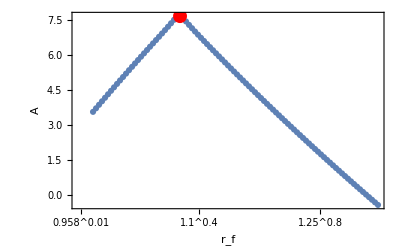

```mathematica
(*
 plot accuracy at a select theta and order over radial domain
*)


 orderIndex=90;
If[orderIndex<= maxSeriesOrder,
theTheta=SetPrecision[thetaRange[[35]],1000];
(*theTheta=SetPrecision[thetaRange[[21]],1000];*)

theTheta=SetPrecision[Pi/4,1000];
 theRatioErrorTable=Table[

 theRadius=Rationalize[radiusStart+(radiusRatios[[n]] radiusDif)];
(*theRadius=Rationalize[extendedRadiusStart+(radiusRatios[[n]]extendedRadiusDif),0];*)
zVal=theRadius Exp[I theTheta];

pVal=(Plus@@analyticTerms[[1;;(analyticOrderList[[orderIndex,2]])]])+(Plus@@singularTerms[[1;;(singularOrderList[[orderIndex,2]])]])/.z->zVal;

(*pVal=seriesTable[[orderIndex]]/.z->zVal;*)
wVals=w/.NSolve[$theFunction==0/.z->zVal];
errTable=Abs[#-pVal]&/@ wVals;

pos=Position[errTable,Min[errTable]][[1,1]];
(*{radiusRatios[[n]],errTable[[pos]]//N,-MantissaExponent[errTable[[pos]]][[2]]},*)
{radiusRatios[[n]],errTable[[pos]]//N,-Log[10,errTable[[pos]]]},
{n,5,Length@radiusRatios}
];
maximalAccuracy=MaximalBy[theRatioErrorTable[[All,{1,3}]],Last]//N;
maxPointG=Graphics@{PointSize[0.025],Red,Point@maximalAccuracy[[1]]};
maxPoint3DG2=Graphics3D@{PointSize[0.025],Red,Point@{maximalAccuracy[[1,1]],orderIndex,maximalAccuracy[[1,2]]}};
radiusTicks[n_]:=radiusRange[[1]]+(radiusRatios[[n]]radiusDif);
maxRadiusRatio=maximalAccuracy[[1,1]];
Print["maxRadiusRatio: ",maxRadiusRatio//N];
nearRatio=Nearest[radiusRatios,maxRadiusRatio][[1]];
pos=Position[radiusRatios,x_/;x==nearRatio][[1,1]];
Print["Ratio index: ",pos];

maximumAccuracyRadius=radiusStart+(maxRadiusRatio radiusDif);
Print["Maximum accuracy radius: ",maximumAccuracyRadius//N];
Print["Maximum accuracy: ",maximalAccuracy[[1,2]]];
ratioPointsPlot2=ListPlot[theRatioErrorTable[[All,{1,3}]],Frame->True,FrameLabel->{Style["r_f",16,Black,Bold],Rotate[Style["A",16,Black,Bold],-90 Degree]},FrameTicks->{Automatic,{{{0.01,Overscript[N[radiusTicks[1],3], N[1/100,2]]},{0.2,Overscript[N[radiusTicks[20],3], N[20/100,2]]},{0.4,Overscript[N[radiusTicks[40],3], N[40/100,2]]},{0.6,Overscript[N[radiusTicks[60],3], N[60/100,2]]},{0.8,Overscript[N[radiusTicks[80],3], N[80/100,2]]},{1,Overscript[N[radiusTicks[100],3], N[1,2]]}},False}}];
Print[Show[{ratioPointsPlot2,maxPointG},FrameTicksStyle->Directive[Black,Bold]]];
,
Print[Style["Order greater than max order "<>ToString@maxSeriesOrder,Red]];
];
```

### Section 5.4: Illustrate inflection point hypothesis

```mathematica
(*
 Compile data
*)
analyticSet=analyticTerms;
singularSet=singularTerms;
mTable3=Table[
theRadius=Rationalize[radiusStart+(radiusRatios[[theN]]radiusDif),0];
theTheta=SetPrecision[Pi/2,1000];
zVal=theRadius Exp[I theTheta];

analTerm=analyticSet[[(analyticOrderList[[orderIndex,2]])]]/.z->zVal;
singTerm=singularSet[[(singularOrderList[[orderIndex,2]])]]/.z->zVal;


aValIm=Im@analyticSet[[(analyticOrderList[[orderIndex,2]])]]/.z->zVal;
sValIm=Im@singularSet[[(singularOrderList[[orderIndex,2]])]]/.z->zVal;
aValRe=Re@analyticSet[[(analyticOrderList[[orderIndex,2]])]]/.z->zVal;
sValRe=Re@singularSet[[(singularOrderList[[orderIndex,2]])]]/.z->zVal;

aValImME=MantissaExponent[aValIm][[2]];
sValImME=MantissaExponent[sValIm][[2]];

aValReME=MantissaExponent[aValRe][[2]];
sValReME=MantissaExponent[sValRe][[2]];

analMan=Abs@analTerm;
singMan=Abs@singTerm;


{orderIndex,aValImME,sValImME,theRadius,aValIm,sValIm,aValRe,sValRe,aValReME,sValReME,analMan,singMan},
{theN,2,95},
{orderIndex,2,maxSeriesOrder-5}
];
```

```mathematica
Manipulate[
Switch[type,
"Re",Column[{Row[{"Radius: ",mTable3[[theN,1,4]]//N}],ListLogPlot[{mTable3[[theN,All,{1,7}]],mTable3[[theN,All,{1,8}]]},PlotRange->{{0,maxSeriesOrder},{10^-25,0}},PlotStyle->{{PointSize[0.01],Blue},{PointSize[0.01],Red}},ImageSize->300,FrameTicksStyle->Directive[Black,Bold,20],(*AxesLabel->{Style[,14,Bold,Black],Rotate[Style["|c_n|",14,Black,Bold],-Pi/2]},*)Frame->True,FrameLabel->{Style[,14,Bold,Black],Rotate[Style["|c_n|",14,Black,Bold],-Pi/2]}]},Alignment->Center],
"Im",Column[{Row[{"Radius: ",mTable3[[theN,1,4]]//N}],ListLogPlot[{mTable3[[theN,All,{1,5}]],mTable3[[theN,All,{1,6}]]},PlotRange->{{0,maxSeriesOrder},{10^-95,0}},PlotStyle->{Blue,Red},PlotRange->All,ImageSize->300,Frame->True,FrameLabel->{Style[,14,Bold,Black],Rotate[Style["|c_n|",14,Black,Bold],-Pi/2]}]},Alignment->Center],
"ReME",
Column[{Row[{"Radius: ",mTable3[[theN,1,4]]//N}],ListPlot[{mTable3[[theN,All,{1,9}]],mTable3[[theN,All,{1,10}]]},PlotRange->{{0,maxSeriesOrder},{-50,0}},PlotStyle->{Blue,Red},PlotRange->All,ImageSize->300]},Alignment->Center],
"ImME",
Column[{Row[{"Radius: ",mTable3[[theN,1,4]]//N}],ListPlot[{mTable3[[theN,All,{1,2}]],mTable3[[theN,All,{1,3}]]},PlotRange->{{0,maxSeriesOrder},{-50,0}},PlotStyle->{Blue,Red},PlotRange->All,ImageSize->300]},Alignment->Center],
"Abs",
Column[{Row[{"Radius: ",mTable3[[theN,1,4]]//N}],ListLogPlot[{mTable3[[theN,All,{1,11}]],mTable3[[theN,All,{1,12}]]},PlotRange->{{0,maxSeriesOrder},{10^-17,0}},PlotStyle->{Blue,Red},PlotRange->All,ImageSize->300,Frame->True,FrameLabel->{Style[,14,Bold,Black],Rotate[Style["|c_n|",14,Black,Bold],-Pi/2]},FrameTicksStyle->Directive[Black,Bold,12]]},Alignment->Center]


],
{{theN,1},1,Length@mTable3,1},{type,{"Re","Im","ReME","ImME","Abs"}},(*ContinuousAction->False,*)ContentSize->400
]
```

Part::partd: Part specification mTable3⟦36,1,4⟧ is longer than depth of object.

Part::partd: Part specification mTable3⟦36,All,{1,7}⟧ is longer than depth of object.

Part::partd: Part specification mTable3⟦36,All,{1,8}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

### Section 5.5: Illustrate accuracy effects near singular points

The radius: 1.31078

test

{{-3.07813,15.708},{-0.309586,1.10127}}

preIndexes: {9,10}

current red Arg: -1.36048

current red Arg: 1.36048

current red Arg: 4.92271

current red Arg: 7.64366

current red Arg: 11.2059

current red Arg: 13.9268

postIndexes: {12}

current blue Arg: 0.

current blue Arg: 6.28319

current blue Arg: 12.5664

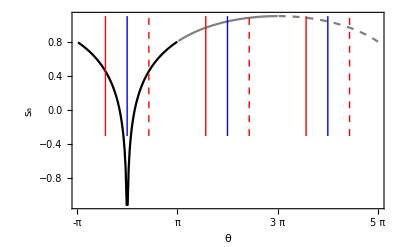

```mathematica
(*
 plot accuracy verses argument from -Pi to Pi for a selected radius
*)
theRadius=SetPrecision[radiusRange[[1]]+(radiusRatios[[95]] radiusDif),1000];
(*
 get bordering singular points
*)
Print["The radius: ",theRadius//N];



 theRatioErrorTable=Table[

theTheta=SetPrecision[thetaRange[[thetaIndex]],1000];
zVal=theRadius Exp[I theTheta];

(*pVal=(Plus@@reducedAnalyticTerms[[1;;analyticOrderIndexList[[orderIndex,2]]]])+(Plus@@theReformedSingularTerms[[1;;singularOrderIndexList[[orderIndex,2]]]])/.z->zVal;*)
pVal=branchSheetF[zVal,n];
wVals=w/.NSolve[$theFunction==0/.z->zVal];
errTable=Abs[#-pVal]&/@ wVals;

pos=Position[errTable,Min[errTable]][[1,1]];
{theTheta+2 n Pi,errTable[[pos]]//N,-Log[10,errTable[[pos]]]},
{n,0,$selectedBranchSize-1},
{thetaIndex,2,Length@thetaRange}
];
Print["test"];
ratioPointsPlot=ListPlot[Flatten[theRatioErrorTable,1][[All,{1,3}]],Frame->True,FrameLabel->{Style["r_f",16,Black,Bold],Rotate[Style["Log_10[s_a]",16,Black,Bold],-90 Degree]},Joined->True];
pRange=PlotRange[ratioPointsPlot]
branchColors={Black,Gray,{Dashed,Gray}};
{aIndex,preIndexes}=getSingTableIndexes[annulusTable,$selectedAnnulus-1];
Print["preIndexes: ",preIndexes];
preLines=Table[
currentSing=$theSingularList[[annulusTable[[preIndexes[[n]],2]]]];
currentArg=Arg[currentSing];
Print["current red Arg: ",currentArg+2 argOffset Pi//N];
If[n==1,
Graphics@{Red,Line[{{currentArg+2 argOffset Pi,pRange[[2,1]]},{currentArg+2 argOffset Pi,pRange[[2,2]]}}]}
,
Graphics@{Dashed,Red,Line[{{currentArg+2 argOffset Pi,pRange[[2,1]]},{currentArg+2 argOffset Pi,pRange[[2,2]]}}]}
]
,
{argOffset,0,$selectedBranchSize-1},
{n,1,Length@preIndexes}
];
{aIndex,postIndexes}=getSingTableIndexes[annulusTable,$selectedAnnulus];
Print["postIndexes: ",postIndexes];
postLines=Table[
currentSing=$theSingularList[[annulusTable[[postIndexes[[n]],2]]]];
currentArg=Arg[currentSing];
Print["current blue Arg: ",currentArg+2 argOffset Pi//N];
Graphics@{Blue,Line[{{currentArg+2 argOffset Pi,pRange[[2,1]]},{currentArg+2 argOffset Pi,pRange[[2,2]]}}]},
{argOffset,0,$selectedBranchSize-1},
{n,1,Length@postIndexes}
];
ratioPointsPlotTable=Table[
ListPlot[theRatioErrorTable[[n,All,{1,3}]],Frame->True,FrameLabel->{Style["θ",16,Black,Bold],Rotate[Style["s_a",16,Black,Bold],-90 Degree]},Joined->True,FrameTicks->{{Automatic,None},{{-Pi,-π},{0,0},{Pi,π},{2 Pi,2 π},{3 Pi,3 π},{4 Pi,4 π},{5 Pi,5 π}}},PlotStyle->branchColors[[n]],FrameTicksStyle->Directive[Black,Bold,12]],
{n,1,$selectedBranchSize}
];
Show[{ratioPointsPlotTable,preLines,postLines},PlotRange->All,Axes->None]
```

### Section 5.6: Generate 3D V-plot of accuracy as a function of radius ratio and order

#### Section 5.6.1: Create 3D accuracy points

```mathematica
(*
 check accuracy across domain 
*)
diagFlag=False;
seriesType=1;

theTheta=SetPrecision[thetaRange[[20]],1000];
theTheta=Arg[$theSingularList[[2]]];
theTheta=SetPrecision[Pi/3,1000];
orderStart=20;
orderEnd=maxSeriesOrder;
plotTable=ParallelTable[
If[Mod[radiusIndex,10]==0,
Print["rIndex: ",radiusIndex];
];
 theOrderErrorTable=Table[
theRadius=radiusStart+(radiusRatios[[radiusIndex]] radiusDif);
zVal=SetPrecision[theRadius Exp[I (theTheta)],1000];
(*pVal=(Plus@@reducedAnalyticTerms[[1;;analyticOrderIndexList[[orderIndex,2]]]])+(Plus@@theReformedSingularTerms[[1;;singularOrderIndexList[[orderIndex,2]]]])/.z->zVal;*)

pVal=seriesTable[[orderIndex]]/.z->zVal;

wVals=w/.NSolve[$theFunction==0/.z->zVal,WorkingPrecision->200];
errTable=Abs[#-pVal]&/@ wVals;
minError=Min@errTable;
If[minError<10^-200,
Print[Style["Error approaching working precision",Red]];
];

pos=Position[errTable,Min[errTable]][[1,1]];
(*{radiusRatios[[n]],errTable[[pos]]//N,-MantissaExponent[errTable[[pos]]][[2]]},*)
{theRadius,orderIndex,-Log[10,errTable[[pos]]]},
{orderIndex,20,maxSeriesOrder,5}
];

cTable=theOrderErrorTable[[All,{2,3}]]//N;
dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];
 (* 
   Fit data to upper minimize function
 *)
linearLine=c0+c1 x/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)>=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)>=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};

functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
(*If[diagFlag,
Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
];
*)

bestUpperFitPlot=Plot[functionList[[bestFitPos]],{x,orderStart,orderEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
bestUpperFitFunction=functionList[[bestFitPos]];
  (* 
   Fit data to lower minimize function
 *)
cTable=theOrderErrorTable[[All,{2,3}]]//N;
dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];
linearLine=c0+c1 x/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
(*If[diagFlag,
Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
];*)



bestLowerFitPlot=Plot[functionList[[bestFitPos]],{x,orderStart,orderEnd},PlotStyle->{Dashed,Thickness[0.0025],Black}];
bestLowerFitFunction=functionList[[bestFitPos]];


{theRadius,{bestLowerFitFunction,bestUpperFitPlot},{bestUpperFitFunction,bestLowerFitPlot},theOrderErrorTable},
{radiusIndex,1,Length@radiusRatios}
];

(*Show[{plotTable[[All,2]]},PlotRange->{{orderStart,plotXEnd},{0,15}}]
*)
```

rIndex: 10

rIndex: 20

rIndex: 30

rIndex: 40

rIndex: 50

rIndex: 60

rIndex: 70

rIndex: 80

rIndex: 90

rIndex: 100

#### Section 5.6.2: Generate 3D point plot

```mathematica
(*
 generate 3D plot
*)
 extRadiusTicks[n_]:=radiusRange[[1]]+(radiusRatios[[n]]radiusDif);

 orderGrids=Array[Floor@#&,{5},{orderStart,orderEnd-2}]

pointPlot3D=ListPointPlot3D[Flatten[plotTable[[All,4]],1],BoxRatios->{1, 1, 1},AxesLabel->{Style["r_f",14,Bold,Black],Style["O",14,Bold,Black],Style["s_a",14,Bold,Black]},AxesEdge->{{1,1},{1,1},{-1,1}},FaceGrids->{{{0,0,1},{{extRadiusTicks[20],extRadiusTicks[40],extRadiusTicks[60],extRadiusTicks[80]},orderGrids}}},

Ticks->{{{extRadiusTicks[1],N[extRadiusTicks[1],2]},{extRadiusTicks[20],N[extRadiusTicks[20],2]},{extRadiusTicks[40],N[extRadiusTicks[40],2]},{extRadiusTicks[60],N[extRadiusTicks[60],2]},{extRadiusTicks[80],N[extRadiusTicks[80],2]},{extRadiusTicks[100],N[extRadiusTicks[100],2]}},orderGrids,Automatic},FaceGridsStyle->Directive[Black,Bold],PlotRange->All,PlotStyle->{PointSize[0.005],Black},TicksStyle->Directive[Black,12,Bold],ViewPoint->{0.5571611020180107,3.136131872804456,-1.1420369445767034},ViewVertical->{0.04822070754259844,0.280016005056937,-0.9587835002105767}]
```

{20,39,58,77,97}

-Graphics3D-

#### Code to return desired view point and view vertical (rotate plot as needed and press Enter)

```mathematica
Options[-Graphics3D-,ViewPoint]
 box=NotebookRead@EvaluationCell[];
Cases[box,(ViewPoint->vp_)|(ViewVertical->vv_):>{vp,vv},Infinity]
```

{ViewPoint→{0.557161,3.13613,-1.14204}}

{{{0.557161,3.13613,-1.14204}},{{0.0482207,0.280016,-0.958784}}}

#### Section 5.6.3: Generate 3D plot with dual x-axis

```mathematica
pointPlot3D=ListPointPlot3D[Flatten[plotTable[[All,4]],1],BoxRatios->{1, 1, 1},AxesLabel->{Style["r_s",14,Bold,Black],Style["O",14,Bold,Black],Style["s_a",14,Bold,Black]},AxesEdge->{{1,1},{1,1},{-1,1}},FaceGrids->{{{0,0,1},{{extRadiusTicks[20],extRadiusTicks[40],extRadiusTicks[60],extRadiusTicks[80]},orderGrids}}},

Ticks->{{{extRadiusTicks[1],Overscript[N[extRadiusTicks[1],2], N[1/100,2]]},{extRadiusTicks[20],Overscript[N[extRadiusTicks[20],2], N[1/20,2]]},{extRadiusTicks[40],Overscript[N[extRadiusTicks[40],2], N[40/100,2]]},{extRadiusTicks[60],Overscript[N[extRadiusTicks[60],2], N[60/100,2]]},{extRadiusTicks[80],Overscript[N[extRadiusTicks[80],2], N[80/100,2]]},{extRadiusTicks[100],Overscript[N[extRadiusTicks[100],2], N[1,2]]}},orderGrids,Automatic},FaceGridsStyle->Directive[Black,Bold],PlotRange->All,PlotStyle->{PointSize[0.005],Black},TicksStyle->Directive[Black,12,Bold]];
Show[{pointPlot3D},ImageSize->300,ViewPoint->{0.5571611020180107,3.136131872804456,-1.1420369445767034},ViewVertical->{0.04822070754259844,0.280016005056937,-0.9587835002105767}]
```

-Graphics3D-

#### Section 5.6.4: Generate interpolation plot

```mathematica
plot5Data=Table[
theF[x_]=plotTable[[rIndex,2,1]];
Table[
{plotTable[[rIndex,1]],o,theF[o]},
{o,orderStart,orderEnd,2}
],
{rIndex,1,Length@plotTable}
];
lpp3D=ListPointPlot3D[Flatten[plot5Data,1],BoxRatios->{1, 1, 1},AxesLabel->{Style["r_s",14,Bold,Black],Style["O",14,Bold,Black],Style["s_a",14,Bold,Black]},AxesEdge->{{1,1},{1,1},{-1,1}}];

 intFA=Interpolation[Flatten[plot5Data,1]];
 intFA=Interpolation[Flatten[plot5Data,1]];
intFPlotA=Plot3D[intFA[r,o],{r,plotTable[[1,1]],plotTable[[-1,1]]},{o,20,maxSeriesOrder},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.25],LightBlue}];

Show[{intFPlotA,lpp3D},AxesLabel->{Style["(r_f,r)",14,Bold,Black],Style[,Bold,Black],Style["s_a",14,Bold,Black]},AxesEdge->{{1,1},{1,1},{-1,1}},FaceGrids->{{{0,0,1},{{extRadiusTicks[20],extRadiusTicks[40],extRadiusTicks[60],extRadiusTicks[80]},orderGrids}}},

Ticks->{{{extRadiusTicks[1],Overscript[N[extRadiusTicks[1],2], N[1/100,2]]},{extRadiusTicks[20],Overscript[N[extRadiusTicks[20],2], N[1/20,2]]},{extRadiusTicks[40],Overscript[N[extRadiusTicks[40],2], N[40/100,2]]},{extRadiusTicks[60],Overscript[N[extRadiusTicks[60],2], N[60/100,2]]},{extRadiusTicks[80],Overscript[N[extRadiusTicks[80],2], N[80/100,2]]},{extRadiusTicks[100],Overscript[N[extRadiusTicks[100],2], N[1,2]]}},orderGrids,Automatic},FaceGridsStyle->Directive[Black,Bold],PlotRange->All,PlotStyle->{PointSize[0.005],Black},ImageSize->300,TicksStyle->Directive[Black,12,Bold],ViewPoint->{0.5571611020180107,3.136131872804456,-1.1420369445767034},ViewVertical->{0.04822070754259844,0.280016005056937,-0.9587835002105767}]
```

-Graphics3D-

### Section 5.7: Check accuracy interpolation function

```mathematica
ratioIndex=50;
selectedOrder=60
theRadius=radiusStart+(radiusRatios[[ratioIndex]] radiusDif);
theTheta=SetPrecision[1/100,1000];
zVal=theRadius Exp[I theTheta];
Print["zVal: ",zVal//N];
Print["theRadius: ",theRadius//N];

(*pVal=(Plus@@reducedAnalyticTerms[[1;;analyticOrderIndexList[[selectedOrder,2]]]])+(Plus@@theReformedSingularTerms[[1;;singularOrderIndexList[[selectedOrder,2]]]])/.z->zVal;*)
pVal1=seriesTable[[selectedOrder]]/.z->zVal;
(*pVal2=seriesTable2/.z->zVal;*)
(*pVal=pureAnalyticSeries[zVal]+pureSingularSeries[zVal];*)
wVals=w/.NSolve[$theFunction==0/.z->zVal];
errTable=Abs[#-pVal1]&/@ wVals;
Print["errTable: ",errTable//N];
pos=Position[errTable,Min[errTable]][[1,1]];
actualError=errTable[[pos]];
Print[Style["Actual accuracy: ",Blue],-Log[10,actualError]//N];
estError=intFA[theRadius,selectedOrder];
Print[Style["Estimated error: ",Red],estError//N];


actErrorG=Graphics3D@{PointSize[0.025],Blue,Point@{theRadius,selectedOrder,-Log[10,actualError]}};

digitsOfAccuracy=MantissaExponent[actualError][[2]];


estErrorG=Graphics3D@{PointSize[0.025],Red,Point@{theRadius,selectedOrder,estError}};

Print["Results: "];
Print["     pVal: ",pVal1//N];
Print["     wVals: ",wVals//N];
Print["     err:   ",errTable//N];

Show[{(*pointPlot3D,*)intFPlotA,actErrorG,estErrorG},AxesLabel->{Style["(r_f,r)",14,Bold,Black],Style[,Bold,Black],Style["s_a",14,Bold,Black]},AxesEdge->{{1,1},{1,1},{-1,1}},FaceGrids->{{{0,0,1},{{extRadiusTicks[20],extRadiusTicks[40],extRadiusTicks[60],extRadiusTicks[80]},orderGrids}}},

Ticks->{{{extRadiusTicks[1],Overscript[N[extRadiusTicks[1],2], N[1/100,2]]},{extRadiusTicks[20],Overscript[N[extRadiusTicks[20],2], N[1/20,2]]},{extRadiusTicks[40],Overscript[N[extRadiusTicks[40],2], N[40/100,2]]},{extRadiusTicks[60],Overscript[N[extRadiusTicks[60],2], N[60/100,2]]},{extRadiusTicks[80],Overscript[N[extRadiusTicks[80],2], N[80/100,2]]},{extRadiusTicks[100],Overscript[N[extRadiusTicks[100],2], N[1,2]]}},orderGrids,Automatic},FaceGridsStyle->Directive[Black,Bold],PlotRange->All,PlotStyle->{PointSize[0.005],Black},ImageSize->300,TicksStyle->Directive[Black,12,Bold],ViewPoint->{0.5571611020180107,3.136131872804456,-1.1420369445767034},ViewVertical->{0.04822070754259844,0.280016005056937,-0.9587835002105767}]
```

60

zVal: 1.14183+0.0114187 ⅈ

theRadius: 1.14189

errTable: {0.00150561,20.6661,20.5467}

Actual accuracy: 2.82229

Estimated error: 3.65342

Results:

pVal: -20.4896-1.05975 ⅈ

wVals: {-20.4908-1.06068 ⅈ,0.0349117+1.35541 ⅈ,0.0548858-1.35874 ⅈ}

err:   {0.00150561,20.6661,20.5467}

-Graphics3D-

## Section 6: Numerical check of accuracy at selected data point

```mathematica
ratioIndex=50;
selectedOrder=80
theRadius=radiusStart+(radiusRatios[[ratioIndex]] radiusDif);
theTheta=SetPrecision[1/100,1000];
zVal=theRadius Exp[I theTheta];
Print["zVal: ",zVal//N];
Print["theRadius: ",theRadius//N];

(*pVal=(Plus@@reducedAnalyticTerms[[1;;analyticOrderIndexList[[selectedOrder,2]]]])+(Plus@@theReformedSingularTerms[[1;;singularOrderIndexList[[selectedOrder,2]]]])/.z->zVal;*)
pVal1=seriesTable[[selectedOrder]]/.z->zVal;
(*pVal2=seriesTable2/.z->zVal;*)
(*pVal=pureAnalyticSeries[zVal]+pureSingularSeries[zVal];*)
wVals=w/.NSolve[$theFunction==0/.z->zVal];
errTable=Abs[#-pVal1]&/@ wVals;
Print["errTable: ",errTable//N];
pos=Position[errTable,Min[errTable]][[1,1]];
actualError=errTable[[pos]];
Print[Style["Actual accuracy: ",Blue],-Log[10,actualError]//N];
estError=intFA[theRadius,selectedOrder];
Print[Style["Estimated error: ",Red],estError//N];


actErrorG=Graphics3D@{PointSize[0.025],Blue,Point@{theRadius,selectedOrder,-Log[10,actualError]}};

digitsOfAccuracy=MantissaExponent[actualError][[2]];


estErrorG=Graphics3D@{PointSize[0.025],Red,Point@{theRadius,selectedOrder,estError}};

Print["Results: "];
Print["     pVal: ",pVal1//N];
Print["     wVals: ",wVals//N];
Print["     err:   ",errTable//N];

Show[{(*pointPlot3D,*)intFPlotA,actErrorG,estErrorG},AxesLabel->{Style["(r_f,r)",14,Bold,Black],Style[,Bold,Black],Style["s_a",14,Bold,Black]},AxesEdge->{{1,1},{1,1},{-1,1}},FaceGrids->{{{0,0,1},{{extRadiusTicks[20],extRadiusTicks[40],extRadiusTicks[60],extRadiusTicks[80]},orderGrids}}},

Ticks->{{{extRadiusTicks[1],Overscript[N[extRadiusTicks[1],2], N[1/100,2]]},{extRadiusTicks[20],Overscript[N[extRadiusTicks[20],2], N[1/20,2]]},{extRadiusTicks[40],Overscript[N[extRadiusTicks[40],2], N[40/100,2]]},{extRadiusTicks[60],Overscript[N[extRadiusTicks[60],2], N[60/100,2]]},{extRadiusTicks[80],Overscript[N[extRadiusTicks[80],2], N[80/100,2]]},{extRadiusTicks[100],Overscript[N[extRadiusTicks[100],2], N[1,2]]}},orderGrids,Automatic},FaceGridsStyle->Directive[Black,Bold],PlotRange->All,PlotStyle->{PointSize[0.005],Black},ImageSize->300,ViewPoint->{0.5571611020180107,3.136131872804456,-1.1420369445767034},ViewVertical->{0.04822070754259844,0.280016005056937,-0.9587835002105767},TicksStyle->Directive[Black,12,Bold]]
```

80

zVal: 0.845375+0.00845403 ⅈ

theRadius: 0.845417

errTable: {3.72346×10^-21,2.61962,2.61796}

Actual accuracy: 20.4291

Estimated error: 20.3942

Results:

pVal: -1.80354+0.0134508 ⅈ

wVals: {-1.80354+0.0134508 ⅈ,0.70379-0.745289 ⅈ,0.707697+0.753325 ⅈ}

err:   {3.72346×10^-21,2.61962,2.61796}

-Graphics3D-

## Section 7: Generate series plots and compare to differential plots

### Section 8.1: Generate series plots for inner annular branches

```mathematica
{analyticTerms,analyticOrderList,singularTerms,singularOrderList} =Import[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,theBranchMonodromy]];
maxAnalyticOrder=analyticOrderList[[-1,1]]
maxSingularOrder=singularOrderList[[-1,1]]
maxSeriesOrder=Min[maxAnalyticOrder,maxSingularOrder]
```

100

199

100

```mathematica
plotDomainDif=2;
branchColors={Red,Blue,Green,Yellow};

  plotDomain=plottingRadiiTable[[$selectedAnnulus]];
rMin=plotDomain[[plotDomainDif]];
rMax=plotDomain[[-plotDomainDif]];
orderIndex=24;
truncatedSeries[z_]:=(Plus@@analyticTerms[[1;;analyticOrderList[[orderIndex,2]]]])+(Plus@@singularTerms[[1;;singularOrderList[[orderIndex,2]]]]);


 theexp=Exponent[truncatedSeries[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[truncatedSeries[z],z,theexp];
(*branchSheetF[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/theCurrentBranchSize])^(theCurrentBranchSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];
*)
branchSheetF[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ theexp[[n]]]) z^theexp[[n]],{n,1,Length[clist]}];

theSeriesPlots=Table[
ParametricPlot3D[{Re@z,Im@z,$plotType@branchSheetF[z,sheetIndex]}/.z->r Exp[I t],{r,rMin,rMax},{t,-Pi,Pi},PlotStyle->branchColors[[sheetIndex+1]],BoxRatios->{1, 1, 2},PlotRange->thePlotRange],
{sheetIndex,0,theCurrentBranchSize-1}
];
```

```mathematica
(* 
overlay series plots with differential plots to compare if equivalent
*)
Show[{theSeriesPlots,theDifferentialPlot},BoxRatios->{1,1,2},Axes->True,AxesLabel->{Style["Re(z)",14,Bold,Black],Style["Im(z)",14,Bold,Black],Style[ ToString[$plotType]<>"(w)",14,Black,Bold]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{0,0,-1}},FaceGridsStyle->Directive[Black,Bold],ImageSize->300]
```

-Graphics3D-

### Section 8.2: Generate series plots for outer annular branches

```mathematica
Print["Importing ",combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,theBranchMonodromy]];
 {analyticTerms,analyticOrderList,singularTerms,singularOrderList} =Import[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,theBranchMonodromy]];
extALen=Length@analyticTerms;
If[extALen==0,
Print[Style["This branch expansion has no analytic terms",Red]];
,
Print["Size of analytic Terms: ",Length@analyticTerms," prec: ",Precision@analyticTerms];
Print["Size of singular terms: ",Length@singularTerms," prec: ",Precision@singularTerms];
If[0<extALen<5,
Print[analyticTerms[[extALen]]//N];
,
Print[analyticTerms[[1;;5]]//N];
];
Print[singularTerms[[1;;7]]//N];
];
Print["The extendedDomain: ",extendedDomain//N]

maxSeriesOrder=singularOrderList[[-1,1]]
```

Importing D:\puiseuxSeries\testCase0008\a7b23combinedExpansionTerms.m

This branch expansion has no analytic terms

The extendedDomain: {9.14715,13.1472}

101

```mathematica
(*
 check if this is the last annular domain 
*)
If[$selectedAnnulus==Length@theAnnuli,
(* this is the last annulus, tack on the analytic terms to singular terms *)
maxSeriesOrder=singularOrderList[[-1,1]];
seriesTable=Table[(Plus@@analyticTerms)+(Plus@@singularTerms[[1;;singularOrderList[[orderIndex,2]]]]),
{orderIndex,1,maxSeriesOrder}
];
Print["Setting max series order to singular terms order"];
,
(* otherwise, set max series order to lesser of analytic and singular orders *)
maxAnalyticOrder=analyticOrderList[[-1,1]];
maxSingularOrder=singularOrderList[[-1,1]];
maxSeriesOrder=Min[maxAnalyticOrder,maxSingularOrder];
Print["maxSeriesOrder: ",maxSeriesOrder];
seriesTable=Table[(Plus@@analyticTerms[[1;;analyticOrderList[[orderIndex,2]]]])+(Plus@@singularTerms[[1;;singularOrderList[[orderIndex,2]]]]);
,
{orderIndex,1,maxSeriesOrder}
];
];
finalReducedSeries[z_]=(Plus@@analyticTerms)+(Plus@@singularTerms);
 theexp=Exponent[finalReducedSeries[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[finalReducedSeries[z],z,theexp];
branchSheetF[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/$selectedBranchSize])^($selectedBranchSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];
```

Setting max series order to singular terms order

```mathematica
plotDomainDif=2;
branchColors={Red,Blue,Green,Yellow};

  plotDomain=plottingRadiiTable[[$selectedAnnulus]];
rMin=plotDomain[[plotDomainDif]];
rMax=plotDomain[[-plotDomainDif]];
orderIndex=75;
(*truncatedSeries[z_]:=(Plus@@analyticTerms[[1;;analyticOrderList[[orderIndex,2]]]])+(Plus@@singularTerms[[1;;singularOrderList[[orderIndex,2]]]]);
*)
(*truncatedSeries[z_]:=(Plus@@singularTerms[[1;;singularOrderList[[orderIndex,2]]]]);*)
truncatedSeries[z_]:=seriesTable[[orderIndex]];
 theexp=Exponent[truncatedSeries[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[truncatedSeries[z],z,theexp];
branchSheetF[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/$selectedBranchSize])^($selectedBranchSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];

theSeriesPlots=Table[
ParametricPlot3D[{Re@z,Im@z,Re@branchSheetF[z,sheetIndex]}/.z->r Exp[I t],{r,rMin,rMax},{t,-Pi,Pi},PlotStyle->{Opacity[0.5],White},BoxRatios->{1, 1, 1},PlotRange->All],
{sheetIndex,0,$selectedBranchSize-1}
];
```

```mathematica
(* check that series plots overlays differential plot *)
Show[{theSeriesPlots,theDifferentialPlot},BoxRatios->{1,1,2},Axes->True,AxesLabel->{Style["Re(z)",14,Bold,Black],Style["Im(z)",14,Bold,Black],Style[ ToString[$plotType]<>"(w)",14,Black,Bold]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{0,0,-1}},FaceGridsStyle->Directive[Black,Bold],ImageSize->300]
```

-Graphics3D-

## Some additional plots

#### Generate full v-shaped accuracy plot using full branchSheetF series

```mathematica
(*
 plot accuracy verses argument from -Pi to Pi for a selected radius
*)

 theAngularErrorTable3D=Table[
theRadius=SetPrecision[radiusRange[[1]]+(radiusRatios[[rIndex]] radiusDif),1000];
(*theRadius=Rationalize[radiusRange[[1]]+(radiusRatios[[rIndex]] radiusDif),0];
*)
theTheta=SetPrecision[thetaRange[[thetaIndex]],1000];
zVal=SetPrecision[theRadius Exp[I theTheta],1000];

pVal=branchSheetF[zVal,n];
wVals=w/.NSolve[$theFunction==0/.z->zVal];
errTable=Abs[#-pVal]&/@ wVals;

pos=Position[errTable,Min[errTable]][[1,1]];
{radiusRatios[[rIndex]],theTheta+2 n Pi,errTable[[pos]]//N,Log[10,errTable[[pos]]]},
{rIndex,5,95},
{n,0,$selectedMonodromyIndexCycleSize-1},
{thetaIndex,2,Length@thetaRange}
];


 pointTable=Flatten[theAngularErrorTable3D,2];
pointTablePlot=ListPointPlot3D[pointTable[[All,{1,2,4}]],BoxRatios->{1, 1, 1},AxesLabel->{Style["r",14,Bold,Black],Style["θ",14,Bold,Black],Style["Log_10[s_a]",14,Bold,Black]},(*FaceGrids->{{0,0,-1}}*)FaceGrids->{{{0,0,-1},{{0},{-Pi,0,Pi,2 Pi,3 Pi}}}},FaceGridsStyle->Directive[Black,Bold],Ticks->{Automatic,{{-Pi,-π},{0,0},{Pi,π},{2 Pi,2π},{3 Pi,3 π}},Automatic},AxesEdge->{{-1,-1},{-1,-1},{1,-1}}  ]
```

-Graphics3D-

```mathematica
pointTablePlotB=ListPointPlot3D[pointTable[[All,{1,2,4}]],BoxRatios->{1, 1, 1},AxesLabel->{Style["r_f",14,Bold,Black],Style["θ",14,Bold,Black],Style["s_a",14,Bold,Black]},(*FaceGrids->{{0,0,-1}}*)FaceGrids->{{{0,0,-1},{{0.2,0.4,0.6,0.8},{-Pi,0,Pi,2 Pi,3 Pi,4 Pi,5 Pi}}}},FaceGridsStyle->Directive[Black,Bold],Ticks->{Automatic,{{-Pi,-π},{0,0},{Pi,π},{2 Pi,2π},{3 Pi,3 π},{4 Pi,4 π},{5 Pi,5 π}},{0.2,0.4,0.6,0.8}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},PlotStyle->{Black}]
```

-Graphics3D-

#### Generate interpolation function of v-plot

```mathematica
intFPointTableB=Interpolation[pointTable[[All,{1,2,4}]]];
intFPlotPointTableB=Plot3D[intFPointTableB[r,θ],{r,radiusRatios[[5]],radiusRatios[[95]]},{θ,thetaRange[[2]],thetaRange[[-1]]+4 Pi},BoxRatios->{1, 1, 1},PlotStyle->LightBlue];
radiusThetaPlot3D=Show[{pointTablePlot,intFPlotPointTableB},Framed->True,AxesLabel->{Style["r_s",14,Bold,Black],Style["θ",14,Bold,Black],Style["A",14,Bold,Black]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{0,0,-1}},FaceGridsStyle->Directive[Black,Bold]]
```

-Graphics3D-

### Check accuracy at constant radius as a function of order

theRadius: 0.468027

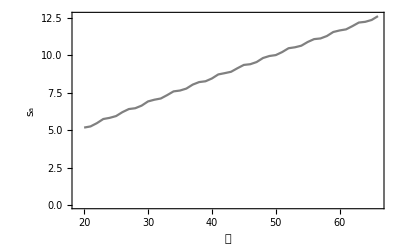

```mathematica
(*
 check accuracy across order range 
*)
radiusIndex=13;
theTheta=Pi;
theRadius=radiusStart+(radiusRatios[[radiusIndex]] radiusDif);
Print["theRadius: ",theRadius//N];
zVal=SetPrecision[theRadius Exp[I (theTheta)],1000];
 theOrderErrorTable=Table[
If[Mod[orderIndex,100]==0,
Print["index: ",orderIndex];
];
(*pVal=(Plus@@reducedAnalyticTerms[[1;;analyticOrderIndexList[[orderIndex,2]]]])+(Plus@@theReformedSingularTerms[[1;;singularOrderIndexList[[orderIndex,2]]]])/.z->zVal;*)
pVal=seriesTable[[orderIndex]]/.z->zVal;
wVals=w/.NSolve[$theFunction==0/.z->zVal,WorkingPrecision->100];
errTable=Abs[#-pVal]&/@ wVals;

pos=Position[errTable,Min[errTable]][[1,1]];
(*{radiusRatios[[n]],errTable[[pos]]//N,-MantissaExponent[errTable[[pos]]][[2]]},*)
{orderIndex,errTable[[pos]]//N,-Log[10,errTable[[pos]]],theTheta},
{orderIndex,20,maxSeriesOrder}
];

orderPointsPlot=ListPlot[theOrderErrorTable[[All,{1,3}]],Frame->True,FrameLabel->{Style["𝒪",16,Black,Bold],Rotate[Style["s_a",16,Black,Bold],-90 Degree]},PlotStyle->Gray,Joined->True,FrameTicksStyle->Directive[Black,Bold,12]]
pRange=PlotRange@orderPointsPlot;
```

#### Fit order data to an upper minimize function

4.35457

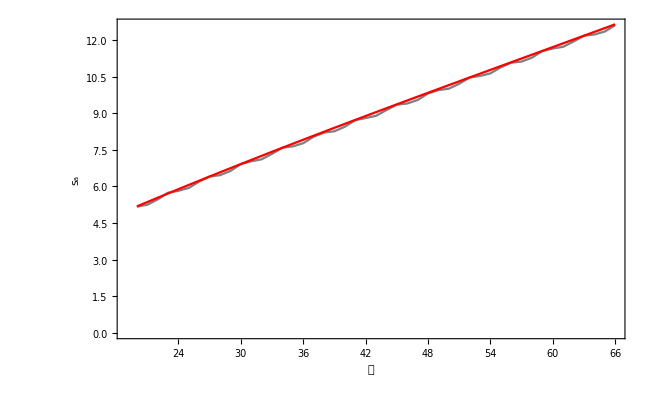

```mathematica
(* 
   Fit data to upper minimize function
 *)
cTable=theOrderErrorTable[[5;;,{1,3}]]//N;
startTerms=10;
dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];
endTerms=Length@cTable;
diagFlag=False;
linearLine=c0+c1 x/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)>=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)>=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals)
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
If[diagFlag,
Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
];

bestUpperFitPlot=Plot[functionList[[bestFitPos]],{x,20,theMaxOrder},PlotStyle->{Thickness[0.0025],Red}];
Show[{orderPointsPlot,bestUpperFitPlot}]
```

#### Fit order data to a lower minimize function

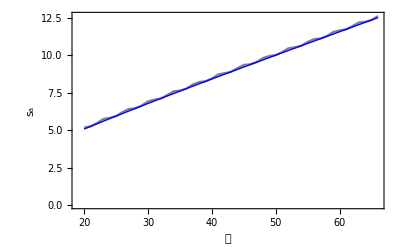

```mathematica
(* 
   Fit data to lower minimize function
 *)
cTable=theOrderErrorTable[[All,{1,3}]]//N;

dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];


linearLine=c0+c1 x/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

logLine=c0+c1 Log[x]/. NMinimize[{Total[(#[[2]]-(c0+c1 Log[#[[1]]]))&/@ dataVals],And@@(((c0+c1 Log[#[[1]]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
logResidue=Plus@@(Abs[#[[2]]-logLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue,logResidue};


functionList={linearLine,quadraticLine,cubicLine,logLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
If[diagFlag,
Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
];

bestLowerFitPlot=Plot[functionList[[bestFitPos]],{x,20,theMaxOrder},PlotStyle->{Thickness[0.0025],Blue}];
Show[{orderPointsPlot,bestLowerFitPlot}]
```

### Manipulate of 4D plot of accuracy profile over entire branch domain

```mathematica
thetaList=Array[#&,25,{-Pi,Pi}]
seriesType=1;
thePlotList1=Table[
Print["theta: ",theta];
 theOrderErrorTable=Table[
theRadius=radiusRange[[1]]+(radiusRatios[[radiusIndex]] radiusDif);
zVal=SetPrecision[theRadius Exp[I (theta)],1000];
If[Mod[radiusIndex,10]==0 && orderIndex==100,
Print["radius index: ",radiusIndex];
];
If[seriesType==1,
pVal=seriesTable[[orderIndex]]/.z->zVal;
,
pVal=seriesTable2[[orderIndex]]/.z->zVal;
];

wVals=w/.NSolve[$theFunction==0/.z->zVal,WorkingPrecision->20];
errTable=Abs[#-pVal]&/@ wVals;

pos=Position[errTable,Min[errTable]][[1,1]];
(*{radiusRatios[[n]],errTable[[pos]]//N,-MantissaExponent[errTable[[pos]]][[2]]},*)
{radiusRatios[[radiusIndex]],orderIndex,Log[10,errTable[[pos]]]},
{radiusIndex,5,55,1},
{orderIndex,100,1000,5}
];
ListPointPlot3D[Flatten[theOrderErrorTable,1],BoxRatios->{1, 1, 1},AxesLabel->{Style["r_s",14,Bold,Black],Style["O",14,Bold,Black],Style["s_a",14,Bold,Black]},AxesEdge->{{1,-1},{-1,-1},{-1,1}},FaceGrids->{{{0,0,-1},{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{200,400,600,800}}}},FaceGridsStyle->Directive[Black,Bold],PlotStyle->{PointSize[0.005],Black},ViewPoint->{6,22,6},PlotRange->{{0,0.5},{100,1000},{-8,1}}],
{theta,thetaList}
];

seriesType=2;
thePlotList2=Table[
Print["theta: ",theta];
 theOrderErrorTable=Table[
theRadius=radiusRange[[1]]+(radiusRatios[[radiusIndex]] radiusDif);
zVal=SetPrecision[theRadius Exp[I (theta)],1000];
If[Mod[radiusIndex,10]==0 && orderIndex==100,
Print["radius index: ",radiusIndex];
];
If[seriesType==1,
pVal=seriesTable[[orderIndex]]/.z->zVal;
,
pVal=seriesTable2[[orderIndex]]/.z->zVal;
];

wVals=w/.NSolve[$theFunction==0/.z->zVal,WorkingPrecision->20];
errTable=Abs[#-pVal]&/@ wVals;

pos=Position[errTable,Min[errTable]][[1,1]];
(*{radiusRatios[[n]],errTable[[pos]]//N,-MantissaExponent[errTable[[pos]]][[2]]},*)
{radiusRatios[[radiusIndex]],orderIndex,Log[10,errTable[[pos]]]},
{radiusIndex,5,55,1},
{orderIndex,100,1000,5}
];
ListPointPlot3D[Flatten[theOrderErrorTable,1],BoxRatios->{1, 1, 1},AxesLabel->{Style["r_s",14,Bold,Black],Style["O",14,Bold,Black],Style["s_a",14,Bold,Black]},AxesEdge->{{1,-1},{-1,-1},{-1,1}},FaceGrids->{{{0,0,-1},{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{200,400,600,800}}}},FaceGridsStyle->Directive[Black,Bold],PlotStyle->{PointSize[0.005],Black},ViewPoint->{6,22,6},PlotRange->{{0,0.5},{100,1000},{-8,1}}],
{theta,thetaList}
];
```

```mathematica
fullPlotList=Join[thePlotList1,thePlotList2[[2;;]]];
Length@fullPlotList
fullThetaList=Join[thetaList,2Pi+thetaList[[2;;]]]
Export[fullAccuracyAnimationFileName[$selectedAnnulus,$selectedMonodromyIndex],{fullPlotList,fullThetaList}];
```

```mathematica
Manipulate[
Column[{Style[fullThetaList[[index]],12], Show[fullPlotList[[index]]]}],
{{index,1},1,Length@fullPlotList,1},ContentSize->{400,400}
]
```

## Generate color-coded accuracy tables

```mathematica
MantissaExponent[Abs[theBaseVal-theSeriesVal]]
```

{0.844715371606236914887801903251227914452192242034868582550566024365491134111127959601095806703205653520471581576541229880404219415423022634602585,-76}

```mathematica
theSeriesVal=Coefficient[theDeletedF[z],z,70];
theBaseVal=Coefficient[baseSeries[[3]],z,70];
theBaseVal//N
theSeriesVal//N


realBaseVal=Re@theBaseVal;
imagBaseVal=Im@theBaseVal;
maxDisplayChar=130;
actWChar=convertToChar[SetPrecision[realBaseVal,maxDisplayChar]]
actWCharRow={Style[70,8],Style[Row[actWChar[[1;;maxDisplayChar]]],8]}


realSeriesVal=Re@theSeriesVal;
imagSeriesVal=Im@theSeriesVal;
seriesWChar=convertToChar[SetPrecision[realSeriesVal,maxDisplayChar]]

seriesWCharRow={Style[70,8],Style[Row[seriesWChar[[1;;maxDisplayChar]]],8]}

Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;



maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
maxCharLen=maxDisplayChar;
i=1;
dotValue=0;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
If[actWChar[[i]]==".",
dotValue=i;
];
];

Print["i: ",i];
Print["dotValue: ",dotValue];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];

For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];
Print["total precision: ",i];
errorData={{Style[70,8],Style[Row[actWChar[[1;;maxDisplayChar]]],8]},
{Style[70,8],Style[Row[seriesWChar[[1;;maxDisplayChar]]],8]}}
```

-7.52976×10^29

-7.52976×10^29

{-,7,5,2,9,7,6,1,5,6,9,4,2,9,2,9,9,4,7,8,8,5,6,8,5,1,1,7,4,4,8,.,4,0,4,8,2,5,7,3,9,5,3,4,4,5,2,2,3,3,7,7,2,6,0,3,4,5,2,8,2,1,4,4,1,0,5,1,6,6,0,5,5,0,9,2,2,4,8,2,4,9,0,8,0,0,8,6,9,8,1,8,0,6,7,9,4,8,8,4,3,3,5,5,7,0,2,7,1,5,8,4,0,0,9,3,3,1,7,5,4,1,5,8,4,5,8,1,0,3,2,2}

{70,-752976156942929947885685117448.40482573953445223377260345282144105166055092248249080086981806794884335570271584009331754158458103}

{-,7,5,2,9,7,6,1,5,6,9,4,2,9,2,9,9,4,7,8,8,5,6,8,5,1,1,7,4,4,8,.,4,0,4,8,2,5,7,3,9,5,3,4,4,5,2,2,3,3,7,7,2,6,0,3,4,5,2,8,2,1,4,4,1,0,5,1,6,6,0,5,5,0,9,2,2,4,8,2,4,9,0,8,0,0,8,6,9,8,1,8,0,6,7,9,4,8,8,4,3,3,5,5,7,0,2,6,3,1,3,6,8,5,5,6,1,5,6,9,1,7,8,9,3,0,9,2,2,5,2,0}

{70,-752976156942929947885685117448.40482573953445223377260345282144105166055092248249080086981806794884335570263136855615691789309225}

actWChar length: 132

seriesWChar length: 132

i: 108

dotValue: 32

total precision: 108

{{70,-752976156942929947885685117448.40482573953445223377260345282144105166055092248249080086981806794884335570271584009331754158458103},{70,-752976156942929947885685117448.40482573953445223377260345282144105166055092248249080086981806794884335570263136855615691789309225}}

```mathematica
Grid[errorData,Dividers->{{{True}},{True,True,{False},True}},Alignment->Left]
```

70 | -752976156942929947885685117448.40482573953445223377260345282144105166055092248249080086981806794884335570271584009331754158458103
70 | -752976156942929947885685117448.40482573953445223377260345282144105166055092248249080086981806794884335570263136855615691789309225

## Initialization Cell:

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]]

<<ComputationalGeometry`
$HistoryLength=0;
 z;
 w;
 c;
 s;
 $userDirectory="D:\\puiseuxSeries";
 $workingPrecision=1000;
 $thetaV=Pi/6;
 $separationFactor;
 $maxRootVerifyDistance=10^-50;
 $accuracyComparisonFactor=20;
 $ringDelta=1/10000;
 $integrationPartition=1;
 $showPlotLabel=False;
 $useAnalyticCodeArray=False;
 $useSingularCodearray=False;
 $selectedAnnulus=1;
 $selectedMonodromyIndex=1;
 $selectedBranch=1;
 $selectedBranchSize=1;
$plotType=Re;

theTypes={Re,Im}

 DistributeDefinitions[ z,
 w,
 $workingPrecision,
 $separationFactor,
 $thetaV,
 $integrationPartition,
 $showPlotLabel
]
```

{Re,Im}

{$workingPrecision,$thetaV,$integrationPartition,$showPlotLabel}

```mathematica
colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];
theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];

Quiet[Select[Names["System`*"],Attributes[#]==={Protected}&&ColorQ[ToExpression[#]]&]]
{"Black","Blue","Brown","Cyan","Gray","Green","LightBlue","LightBrown","LightCyan","LightGray","LightGreen","LightMagenta","LightOrange","LightPink","LightPurple","LightRed","LightYellow","Magenta","Orange","Pink","Purple","Red","Transparent","White","Yellow"}
colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];

theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];
colorTable=Flatten@theColorList;
colorTable[[1;;10]]={Blue,Red,Yellow,Brown,Cyan,Green,Orange,Pink,Purple,Magenta}
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Magenta,Orange,Pink,Purple,Red,Transparent,White,Yellow}

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Magenta,Orange,Pink,Purple,Red,Transparent,White,Yellow}

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0.6, 0.4, 0.2],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0.5],RGBColor[0.5, 0, 0.5],RGBColor[1, 0, 1]}

### binary packing routines

```mathematica
RealToHex32[x_]:=Module[{tmp},tmp=OpenTemporary[BinaryFormat->True];
BinaryWrite[tmp,x,"Real32"];
tmp=Close[tmp];
{BinaryRead[tmp,"UnsignedInteger8"],BinaryRead[tmp,"UnsignedInteger8"],BinaryRead[tmp,"UnsignedInteger8"],BinaryRead[tmp,"UnsignedInteger8"]}]



floatToBinary[inum_]:=Module[{theSign,ival,theDigits,theexp,mantissa,binExp,packedForm,packedArray},
If[inum<0,
theSign=1;
,
theSign=0;
];
ival=RealDigits[inum,2];
theDigits=PadRight[ival[[1]],32];
theexp=ival[[2]];

mantissa=theDigits[[2;;24]];
If[inum==0,
binExp=IntegerDigits[0,2,8];
,
binExp=IntegerDigits[theexp-1+127,2,8];
];
packedForm=Join[{theSign},binExp,mantissa];
packedArray={FromDigits[packedForm[[25;;32]],2],FromDigits[packedForm[[17;;24]],2],FromDigits[packedForm[[9;;16]],2],FromDigits[packedForm[[1;;8]],2]}
];

packInt32[theNum_]:=Module[{int32},
int32=IntegerDigits[theNum,2,32];
{FromDigits[int32[[25;;32]],2],FromDigits[int32[[17;;24]],2],FromDigits[int32[[9;;16]],2],FromDigits[int32[[1;;8]],2]}
];
```

### polyForm

```mathematica
polyForm[poly_,var_]:=Module[{coeffs=CoefficientRules[poly,var]//Sort},Interpretation[Row[Table[Row[{"(",coeff[[2]],")",var^coeff[[1,1]]/.1->""}],{coeff,coeffs}],"+"],poly]]
```

```mathematica
(* parallelize version *)
 
getRingMonodromy[ringNum_,baseComparisonAccuracy_]:=Module[{precisionArray,rnorm,zstart,theBaseValues,theBaseValueDigits,tStart,tEnd,branchValues,root,wstart,wstartDigits,wDeriv,posFoundFlag,numTries,theCentralTrace,theCentralTraceValueDigits,loopPos,loopPosVal,zStartPrecision,myazsol,aIndex,sIndex},
precisionArray={{1/1000,20},{1/2000,20},{1/3000,20},{1/5000,30},{1/6000,30},{1/7000,30},{1/10000,40},{1/12000,40},{1/15000,40},{1/20000,50},{1/25000,55},{1/30000,55},{1/30000,60}};
  
     (*  For[ringNum=83,ringNum≤Length[ringRegions],ringNum++, *)    

Print[Style["Analyzing ring ",Red],Style[ringNum,Red]];
{aIndex,sIndex}=getSingTableIndexes[annulusTable,ringNum];
rnorm=annulusTable[[aIndex,4]];
(*rnorm=radiiTable[[ringNum,(radialSegments-1)/2+1]];*)
zstart=rnorm Exp[ⅈ $thetaV];
zStartPrecision=Precision[zstart];
theBaseValues=w/.NSolve[$theFunction==0/.z->zstart,w,WorkingPrecision->workingPrecision];
theBaseValues=Sort[theBaseValues,If[Re[#1]!=Re[#2],
Re[#1]<Re[#2]
,
Im[#1]<Im[#2]
]&];
theBaseValueDigits=getDigits[theBaseValues,baseComparisonAccuracy];
tStart=$thetaV;
tEnd=$thetaV+2 π ;
branchValues={};
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (ⅈ rnorm Exp[ⅈ t]))/.{w->w[t],z->rnorm Exp[ⅈ t]});
 (* For[root=4,root≤4,root++, *) 
 For[root=1,root≤functionOrder,root++,  
wstart=theBaseValues[[root]];
wstartDigits=getDigits[wstart,baseComparisonAccuracy]//First;
posFoundFlag=False;
numTries=1;
While[posFoundFlag==False && numTries≤Length[precisionArray],
If[numTries>3,
myazsol=First[NDSolve[{wDeriv,w[tStart]==wstart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]],Method->"StiffnessSwitching"]];
,
myazsol=First[NDSolve[{wDeriv,w[tStart]==wstart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]]]];
];
theCentralTrace[t_]=Evaluate[Flatten[w[t]/.myazsol]];
theCentralTraceValueDigits=getDigits[theCentralTrace[tEnd],baseComparisonAccuracy]//First;
loopPos=Position[theBaseValueDigits,theCentralTraceValueDigits];
If[Length[loopPos]≠1,
Print["Error finding digits for root num ",root," Increasing precision to ",precisionArray[[numTries]]," ",numTries," of 13"];
If[numTries>3,
Print["Switching to StiffnessSwitching method"];
];
,
loopPosVal=loopPos//First;
branchValues=Append[branchValues,{wstartDigits,theBaseValueDigits[[loopPosVal[[1]]]]}];
posFoundFlag=True;
];
numTries++;
];
If[posFoundFlag==False,
Print["Position not found at end of ",Length[precisionArray], " attempts at increasing precision."];
Abort[];
];
];
branchValues
];

(* parallizing versioin *)



getSingularPointMonodromy[singNum_,baseComparisonAccuracy_]:=Module[{precisionArray,rnorm,singularStartArg,zstart,theBaseValues,theBaseValueDigits,tStart,tEnd,wstart,wstartDigits,wDeriv,posFoundFlag,numTries,myazsol,theCentralTrace,theCentralTraceValueDigits,loopPos,branchValues,rmax,root,saveBaseDigits,poleFlag,j,savePoleValues},
precisionArray={{1/1000,20},{1/2000,20},{1/3000,20},{1/5000,30},{1/6000,30},{1/7000,30},{1/10000,40},{1/12000,40},{1/15000,40},{1/20000,50},{1/25000,55},{1/30000,55},{1/30000,60}};
branchValues={};
saveBaseDigits={};
savePoleValues={};
rnorm=$minRadiusArray[[singNum]];
singularStartArg=argList[[singNum]]-π;
Print["Analyzing monodromy around singular point ",singNum, " : ",N[$theSingularList[[singNum]],8]];
zstart=$theSingularList[[singNum]]+$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg];
(*If[singNum==Length[$theSingularList],
Print["Analyzing monodromy around infinity"];
zstart=$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg];
,
Print["Analyzing monodromy around singular point ",singNum, " : ",N[$theSingularList[[singNum]],8]];
zstart=$theSingularList[[singNum]]+$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg];
];*)
theBaseValues=w/.NSolve[$theFunction==0/.z->zstart];
theBaseValues=Sort[theBaseValues,If[Re[#1]!=Re[#2],
Re[#1]<Re[#2]
,
Im[#1]<Im[#2]
]&];
(*Print["theBaseValues: ",theBaseValues//N];*)
theBaseValueDigits=getDigits[theBaseValues,baseComparisonAccuracy];
(* now check if this is a pole *)
poleFlag=False;
If[MemberQ[$poleIndexes,singNum],
poleFlag=True;
AppendTo[savePoleValues,{singNum,theBaseValues}];
];
(*For[j=1,j≤Length[pole2],j++,
If[$theSingularList[[singNum]]==pole2[[j]],
 poleFlag=True;
];
];*)
zstart=$theSingularList[[singNum]]+$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg];
If[poleFlag,
saveBaseDigits=Append[saveBaseDigits,{singNum,$theSingularList[[singNum]]+$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg],$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg]}];
];
tStart=singularStartArg;
tEnd=tStart+2 π;
rmax=Length[theBaseValues];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (ⅈ rnorm Exp[ⅈ t]))/.{w->w[t],z->$theSingularList[[singNum]]+rnorm Exp[ⅈ t]});
For[root=1,root≤rmax,root++,
wstart=theBaseValues[[root]];
wstartDigits=getDigits[wstart,baseComparisonAccuracy]//First;
posFoundFlag=False;
numTries=0;
While[posFoundFlag==False && numTries≤13,
numTries++;
If[numTries>3,
Print["Switching to StiffnessSwitching"];
myazsol=First[NDSolve[{wDeriv,w[tStart]==wstart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]],Method->"StiffnessSwitching"]];
,
myazsol=First[NDSolve[{wDeriv,w[tStart]==wstart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]]]];
];
theCentralTrace[t_]=Evaluate[Flatten[w[t]/.myazsol]];
theCentralTraceValueDigits=getDigits[theCentralTrace[tEnd],baseComparisonAccuracy]//First;
loopPos=Position[theBaseValueDigits,theCentralTraceValueDigits];
If[Length[loopPos]≠1,
Print["Error with loopPos: ",loopPos];
 Print["Base Value digits: ",theBaseValueDigits];
Print["base values: ",theBaseValues//N];
Print["the Central trace Digits: ",theCentralTraceValueDigits]; 
Print["central trace: ",theCentralTrace[tEnd]];
,
branchValues=Append[branchValues,{wstartDigits,theBaseValueDigits[[loopPos[[1,1]]]]}];
posFoundFlag=True;
];
];
If[posFoundFlag==False,
Print["Position not found at end of 10 attempts at increasing precision."];
Abort[];
];
];
{branchValues,saveBaseDigits,savePoleValues}
];
```

### Subroutine call for initialization of data

```mathematica
(* attempt to make sub for init data *)



(* In order to have unique barycentric ids for each vertex, must use radialSegments=3n+1 and odd for vertex calculations to find a mid point*)

radialSegments=13;
(* arcSegments is 2n *)
arcSegments=48;
totalIntegrationSteps=1500000;
maxStepSize=0.0001;
workingPrecision=75;

ringDelta=1/20000; (* ring separation threshold *)
minRingSize=1/2000;

initializationFunction[$theFunction_]:=Module[{singlist,singularPrecision,theValues,polePrecision,newPrecision,sing2,rings,pre,ring2,theRingSet,ringDifferences,i,j,min,distance,preRingSize,postRingSize,newRing,theRingDigits,theSingList,singStyle,index,currentSing,pos},
functionOrder=Exponent[$theFunction,w];
singlist=(z/.NSolve[Resultant[$theFunction,D[$theFunction,w],w]==0,z,WorkingPrecision->workingPrecision]);
singularPrecision=Precision[singlist];

theValues=NSolve[Coefficient[$theFunction,w^functionOrder]==0,z,WorkingPrecision->workingPrecision];
If[Length[theValues]>0,
thePoles=z/.theValues;
polePrecision=Precision[thePoles];
,
thePoles={};
polePrecision=singularPrecision;
];
(* take min of these precison *)
newPrecision=Min[singularPrecision,polePrecision];
Print ["Working precision of computations: ",newPrecision];

sing2=SetPrecision[singlist,newPrecision-2];
pole2=SetPrecision[thePoles,newPrecision-2];
pole2=Sort[DeleteDuplicates[pole2],Abs[#1]≤Abs[#2]&];
sing3=Sort[DeleteDuplicates[sing2],Abs[#1]≤Abs[#2]&];
$theSingularList=sing3;
rings=Sort[Abs[singlist]];
pre=Precision[rings];
ring2=SetPrecision[rings,pre-2];
ring3=Sort[DeleteDuplicates[ring2]];

theRingSet=Union[{0},ring3,{Last[ring3]+4}];
ringRegions=Table[{0,0},{Length[theRingSet]-1}];
For[i=1,i≤Length[theRingSet]-1,i++,
ringRegions[[i,1]]=theRingSet[[i]]+ringDelta;
ringRegions[[i,2]]=theRingSet[[i+1]]-ringDelta;
];

ringDifferences={#[[2]]-#[[1]]}& /@ ringRegions;
If[Length[Select[Flatten[ringDifferences],#<1/5000&]]>1,
Print[Style["Ring size too small",Red]];
Print[Select[Flatten[ringDifferences],#<1/5000&]];
Abort[];
];

radiiTable=Table[Array[#&,radialSegments,ringRegions[[i]]],{i,1,Length[ringRegions]}];

(* need to flag this as an expansion around the origin *)

singularPointExpansion=False;


minArray={};
For[i=1,i≤Length[sing3],i++,
currentSing=sing3[[i]];
min=10^6;
For[j=1,j≤Length[sing3],j++,
If[j≠i,
distance=Sqrt[(Re[currentSing]-Re[sing3[[j]]])^2+(Im[currentSing]-Im[sing3[[j]]])^2];
If[distance<min,
min=distance;
];
];
];
minArray=Append[minArray,min/2];
];
sing3=Append[sing3,0];
(* now add a circle around all singular points for the point at infinity *)
minArray=Append[minArray,Max[ring3]+2];
(* and add zero as the center of this ring.  The added zero at the end allows a spacer so when it gets to this point *)
(* the ring monodromy will be around all finite singular points so is the mondromy around infinity  *)
(* now add zero at end of singular list for point at infinity *)
(*
  now save this copy of min array to use as radius of convergence of power series 
*)

$theSingularList=Append[$theSingularList,0];
theArgList=Map[Arg,$theSingularList];
(*  now that args are computed, switch last singular point to infty *)
$theSingularList[[-1]]=∞;
theSingularListGraphics=MapThread[{#1,#2}&, {Range[Length[$theSingularList]],$theSingularList//N}];

For[i=1,i≤Length[$theSingularList],i++,
For[j=1,j≤Length[pole2],j++,
If[$theSingularList[[i]]==pole2[[j]],
 theSingularListGraphics[[i]]={Style[theSingularListGraphics[[i,1]],Red],Style[theSingularListGraphics[[i,2]],Red]}; 
];
];
];
(* --------------------------------------------------*)
theRingList=MapThread[{#1,#2}&,{Range[Length[ringRegions]],ringRegions}];
theRingListGraphics=MapThread[{#1,#2,#3}&,{Range[Length[ringRegions]],ringRegions//N,ringDifferences//N}];
(* now adjust radius around each finite point to 1/3 minimum distance between rings or to nearest singular point *)
For[i=2,i≤Length[theRingList],i++,
For[j2=1,j2≤Length[$theSingularList],j2++,
If[Abs[$theSingularList[[j2]]]<theRingList[[i,2,1]] && Abs[$theSingularList[[j2]]]>theRingList[[i-1,2,2]],
preRingSize=(theRingList[[i-1,2,2]]-theRingList[[i-1,2,1]])/3;
postRingSize=(theRingList[[i,2,2]]-theRingList[[i,2,1]])/3;
minArray[[j2]]=Min[{minArray[[j2]],preRingSize,postRingSize}];
];
];
];

newRing=Select[ring3,#>0&];
For[i=1,i≤Length[newRing],i++,
newRing[[i]]={newRing[[i]],{}};
];
theRingDigits=getDigits[newRing[[All,1]],10];
theSingList=Select[sing3,Abs[#]>0&];
For[i=1,i≤Length[theSingList],i++,
pos=Position[theRingDigits,getDigits[Abs[theSingList[[i]]],10][[1]]][[1,1]];
singStyle=Style[theSingList[[i]]//N];
For[j=1,j≤Length[pole2],j++,
If[theSingList[[i]]==pole2[[j]],
 singStyle=Style[theSingList[[i]]//N,Red]; 
];
];
newRing[[pos,2]]=Append[newRing[[pos,2]],singStyle];
];

ringDisplay={};
For[i=1,i≤Length[newRing],i++,
ringDisplay=Append[ringDisplay,{i,newRing[[i,1]],newRing[[i,2]]}];
];
finalRingDisplay={};
If[$theSingularList[[1]]==0,
finalRingDisplay=Append[finalRingDisplay,{" "," ",Subscript[s, 0],Style[0,Red]}];
];
index=0;
For[i=1,i≤Length[ringDisplay],i++,
index++;
finalRingDisplay=Append[finalRingDisplay,{Subscript[r, ringDisplay[[i,1]]],ringDisplay[[i,2]]//N,Subscript[s, index],ringDisplay[[i,3,1]]}];
If[Length[ringDisplay[[i,3]]]>1,
For[j=2,j≤Length[ringDisplay[[i,3]]],j++,
index++;
finalRingDisplay=Append[finalRingDisplay,{" "," ",Subscript[s, index],ringDisplay[[i,3,j]]}];
];
];
];
Print[finalRingDisplay//MatrixForm];
];

generateIntegerFunction[zdegree_,wdegree_,maxlim_]:=Module[{thenumber,mylist,aseq,atemp,a,$theFunction},
thenumber=IntegerDigits[RandomInteger[{1,2^((wdegree+1)(zdegree+1))-1}],2,(zdegree+1)(wdegree+1)];
mylist=Table[aseq=Take[thenumber,{(zdegree+1)(n-1)+1,(zdegree +1)n}];
atemp=Table[If[aseq[[j]]≠0,
RandomInteger[{-maxlim,maxlim}]Power[z,j-1],"A"],{j,1,zdegree+1}];
Subscript[a, n-1]=Plus@@DeleteCases[atemp,_String],{n,1,wdegree+1}];
$theFunction=Plus@@Table[Subscript[a, n] w^n,{n,0,wdegree}]
];

generateRationalFunction[zdegree_,wdegree_,maxlim_]:=Module[{thenumber,mylist,aseq,atemp,a,$theFunction,num,denom,theval,temp},
thenumber=IntegerDigits[RandomInteger[{1,2^((wdegree+1)(zdegree+1))-1}],2,(zdegree+1)(wdegree+1)];
mylist=Table[aseq=Take[thenumber,{(zdegree+1)(n-1)+1,(zdegree +1)n}];
atemp=Table[If[aseq[[j]]≠0,
{
num=RandomInteger[{-maxlim,maxlim}];
denom=RandomInteger[{-maxlim,maxlim}];
While[denom==0,
denom=RandomInteger[{-maxlim,maxlim}];
];
theval=num/denom Power[z,j-1];
}
,
theval="A"];
theval,{j,1,zdegree+1}];
Subscript[a, n-1]=Plus@@DeleteCases[atemp,_String],{n,1,wdegree+1}];
$theFunction=Plus@@Table[Subscript[a, n] w^n,{n,0,wdegree}]
];
```

```mathematica
FourierSmooth[Graphics[{___,Style[Line[pts_],___],___}],numFourCoeff_Integer]:=Module[{wx,wy,ftsum,w,nn},If[numFourCoeff<1||numFourCoeff>nn/2,
Return[$Failed]
];
nn=Length[pts];
{wx,wy}=Fourier/@Transpose[pts];
ftsum[t_]:=Evaluate[1/Sqrt[nn](w[1]+Sum[2w[i+1]*Exp[-2Pi I t i/nn],{i,1,numFourCoeff}])];
Show[{
Graphics[{Gray,Dashed,Line[pts]}],
ParametricPlot[Re[ftsum[t]]/.w[i__]:>{wx[[i]],wy[[i]]},{t,0,nn},PlotStyle->{Magenta},Axes->False,Frame->True]
}]
]

FourierSmooth3[Graphics[{___,Line[pts_]}],numFourCoeff_Integer]:=Module[{wx,wy,ftsum,w,nn},
If[numFourCoeff<1||numFourCoeff>nn/2,
Return[$Failed]
];
nn=Length[pts];
Print["total points: ",nn];
{wx,wy}=Fourier/@Transpose[pts];
ftsum[t_]:=Evaluate[1/Sqrt[nn](w[1]+Sum[2w[i+1]*Exp[-2Pi I t i/nn],{i,1,numFourCoeff}])];
Show[{
Graphics[{Gray,Dashed,Line[pts]}],
ParametricPlot[Re[ftsum[t]]/.w[i__]:>{wx[[i]],wy[[i]]},{t,0,nn},PlotStyle->{Magenta},Axes->False,Frame->True]
}]
]


FourierSmooth2[Graphics[Style[Line[pts_],___]],numFourCoeff_Integer]:=Module[{wx,wy,ftsum,w,nn},
If[numFourCoeff<1||numFourCoeff>nn/2,
Return[$Failed]
];
nn=Length[pts];
{wx,wy}=Fourier/@Transpose[pts];
ftsum[t_]:=Evaluate[1/Sqrt[nn](w[1]+Sum[2w[i+1]*Exp[-2Pi I t i/nn],{i,1,numFourCoeff}])];
Show[{
Graphics[{Gray,Dashed,Line[pts]}],
ParametricPlot[Re[ftsum[t]]/.w[i__]:>{wx[[i]],wy[[i]]},{t,0,nn},PlotStyle->{Magenta},Axes->False,Frame->True]
}]
]
getDigitsOld[vals_,n_]:=Module[{net,theDigits,i,theChoppedVals,theComponents,myList},
If[Length[vals]==0,
myList={vals};
,
myList=vals;
];
net=Length[myList];
theChoppedVals=Chop[myList,10^(-n)];
theComponents={Re[#],Im[#]}& /@ theChoppedVals;
theDigits=RealDigits[theComponents,10,n];
For[i=1,i≤net,i++,
If[Re[theChoppedVals[[i]]]<0,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],-1];
,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],1];
];
If[Im[theChoppedVals[[i]]]<0,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],-1];
,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],1];
];
];
theDigits
];
getDigitsOld2[vals_,n_]:=Module[{net,theDigits,i,theChoppedVals,theComponents,myList},
If[Length[vals]==0,
myList={vals};
,
myList=vals;
];
myList=SetAccuracy[myList,2n+2];
net=Length[myList];

theComponents={Re[#],Im[#]}& /@ myList;
theChoppedVals=Chop[theComponents,10^(-n)];
theDigits=RealDigits[theChoppedVals,10,n];
For[i=1,i≤net,i++,
If[theChoppedVals[[i,1]]<0,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],-1];
,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],1];
];
If[theChoppedVals[[i,2]]<0,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],-1];
,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],1];
];
];
theDigits
];

getDigits[vals_,n_]:=Module[{net,theDigits,i,theChoppedVals,theComponents,myList,listAccuracy},
If[Length[vals]==0,
myList={vals};
,
myList=vals;
];
listAccuracy=Accuracy[myList];
(* set accuracy to n+1  to round-off 0.899999 to 0.9 and others *)
myList=SetAccuracy[myList,n+10];
net=Length[myList];

theComponents={Re[#],Im[#]}& /@ myList;
theChoppedVals=Chop[theComponents,10^(-n)];
theDigits=RealDigits[theChoppedVals,10,n];
For[i=1,i≤net,i++,
If[theChoppedVals[[i,1]]<0,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],-1];
,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],1];
];
If[theChoppedVals[[i,2]]<0,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],-1];
,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],1];
];
];
theDigits
];




DistributeDefinitions[{getRingMonodromy,getSingularPointMonodromy,getDigits}];
```

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];
```

### getRandomPoly

```mathematica
zExpMax=2;
wExpMax=3;
sparseVal=1;
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,5}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
$theFunction=Sum[randomNum[sparseVal] getcoef[8,5]z^getZPower[zExpMax] w^getWPower[wExpMax],{wExpMax}]
polyForm[$theFunction,w]
```

-4

++(-4)

```mathematica
getRandomSingleCoeffPoly[3,5,5,2]
```

getRandomSingleCoeffPoly[3,5,5,2]

```mathematica
getRandomSingleCoeffPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,$theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,5}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
$theFunction=Sum[randomNum[sparseVal] getcoef[8,5]z^getZPower[zExpMax] w^getWPower[wExpMax],{wExpMax}];
(*$theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];*)
If[!IrreduciblePolynomialQ[$theFunction],
index++;
,
foundFlag=True;
];
];
$theFunction
]
```

```mathematica
getRandomPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,$theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,n}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
$theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];
If[!IrreduciblePolynomialQ[$theFunction],
index++;
,
foundFlag=True;
];
];
$theFunction
]


getRandomComplexPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,$theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,n}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}]+I RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
$theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];
If[!IrreduciblePolynomialQ[$theFunction],
index++;
,
foundFlag=True;
];
];
$theFunction
]
```

### getZeroIndexes

```mathematica
getZeroIndexes[$theFunction_,theSingularList_,diag_:False]:=Module[{wKeys,a0Rule,a1Rule,theZeroPoints,zeroPrecision,duplicateError,zeroIndexes,theZeroList,singPrecision,difTable,maxDif,rootPrecisionTable,dif},
wKeys=CoefficientRules[$theFunction,w,"NegativeLexicographic"];
a0Rule=Normal@KeyTake[wKeys,{{0},z}];
singPrecision=Floor@Precision@theSingularList;

If[Length@a0Rule>0 ,
(* found a_0 *)
If[Exponent[a0Rule[[1,2]],z]>0,
a1Rule=Normal@KeyTake[wKeys,{{1},z}];
If[Length@a1Rule>0,
(* now have a0 and a1 in function *)
If[Exponent[a1Rule[[1,2]],z]>0,
(* a1 is a poly degree>0 *)
If[a0Rule[[1,2]]===a1Rule[[1,2]],
(* at this point a0===a1 poly degree>0 so zero terms are zeros to a0 *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
,
(*Print[Style["No zero key singular points",Red]];*)
theZeroPoints={};
];
,
(* if a1 is a constant zero set is null *)
theZeroPoints={};
];
,
(* have no a1 at this point *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=a0Rule[[1,2]]/.z->#&/@ theZeroPoints;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];
zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];
];
,
theZeroPoints={};
];
,
theZeroPoints={};
];
If[diag,
Print["theZeroPoints: ",theZeroPoints//N];
];
If[Length@theZeroPoints>0,

zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];

zeroIndexes=Flatten[
Table[
dif=Abs[theZeroList[[i]]-#]&/@ theSingularList;
Position[dif,x_/;x==Min[dif]][[1,1]],
{i,1,Length@theZeroList}
]];
,
zeroIndexes={};

];
zeroIndexes
];
```

### getPoles

```mathematica
getPoles[$theFunction_,theSingularList_,diag_:False]:=Module[{wExpList,poleFunction,pExp,singPrecision,thePoles,polePrecision,thePoleList,poleF,poleIndexes,difTable,maxDif,duplicateError,pTable,rootPrecisionTable},
wExpList=Exponent[$theFunction,w,List];
poleFunction=Coefficient[$theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
(* check if a_n(z) is a polynomial of degree>0 *)
singPrecision=Floor@Precision@theSingularList;
If[Last@pExp>0,
thePoles=Sort[z/.NSolve[Factor@poleFunction==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=poleFunction/.z->#&/@ thePoles;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];

polePrecision=Floor@Precision@thePoles;
duplicateError=Min[polePrecision,singPrecision]-$accuracyComparisonFactor;
thePoleList=DeleteDuplicates[thePoles,Abs[#1-#2]<10^-(duplicateError)&];
,
thePoleList={};
];
poleF[a_]:=(Abs[#-a]&/@ theSingularList);
poleIndexes=Flatten[Position[poleF[#],Min[poleF[#]]]&/@ thePoleList];
poleIndexes
];
```

### getNewSingularData

```mathematica
getNewSingularData[$theFunction_,workingPrecision_:1000,diagFlag_:False]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDist,minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,zeroIndexes,originCheck,argList,absVals,ringSizes,minRingSize,singularListR,annularSizes,ringMembers,polePos,ringMembersR,ringTable,snIndex,ringTableR,theAnnuli,radiiTable,singularRingIndexes
},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn=ConstantArray[-1,12];
,
If[!strictPolynomialQ[$theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn=ConstantArray[-1,12];
,
If[!IrreduciblePolynomialQ[$theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[$theFunction],Red]];
theReturn=ConstantArray[-1,12];
}
,
at1=AbsoluteTiming[
res=Resultant[$theFunction,D[$theFunction,w],w];
];
If[diagFlag,
Print["Time to compute resultant: ",at1[[1]]];
];
at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];
If[diagFlag,
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn=ConstantArray[-1,12];
,
(*
 final form of the singular list
*)
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$accuracyComparisonFactor)&];
(*
 get arguments of singular points
*)
argList=Arg@theSingularList;
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[$theFunction,theSingularList,False];
(*
get poles
*)
poleIndexes=getPoles[$theFunction,theSingularList,False];
(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];
minRadiusArray=nearestDist;
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray=∞;
];
(* 
compute rings
*)
 absVals=Abs@#&/@ theSingularList;
ringSizes=DeleteDuplicates[absVals,Abs[#1-#2]<10^-$accuracyComparisonFactor&];
(*
  compute annular regions (need to adjust them by deltaRing for numerical work )
*)
theAnnuli=Table[
{ringSizes[[i]],ringSizes[[i+1]]},
{i,1,Length@ringSizes-1}];
Print["Total annuli: ",Length@theAnnuli];
minRingSize=Min[Differences[theAnnuli]];

AppendTo[theAnnuli,{ringSizes[[-1]],ringSizes[[-1]]+4}];
Print["theAnnuli: ",theAnnuli//N];
(*
 compute radiiTable
*)
radiiTable=Table[Array[#&,radialSegments,theAnnuli[[i]]],{i,1,Length[theAnnuli]}];
(*singularListR=theSingularList;
(singularListR[[#]]=Style[N[singularListR[[#]],6],Red])&/@poleIndexes;
*)
(*
 compute annular sizes
*) 
annularSizes=Abs[#[[2]]-#[[1]]]&/@ theAnnuli//N;
Print["annularSizes: ",annularSizes//N];
(*
  determine which singular points are on each ring
*)
ringMembers=Table[
Select[theSingularList[[1;;]],Abs[Abs[#]-theAnnuli[[rIndex,1]]]<10^-10&],
{rIndex,1,Length@theAnnuli}
];
(*
 determine position in theSingularList for each ring member
*) 
singularRingIndexes=Table[
Flatten[Position[theSingularList[[1;;]],x_/; Abs[x-#]<10^-10]& /@ ringMembers[[j]]],
{j,1,Length@ringMembers}
];
polePos=Flatten[Position[ringMembers,x_/;Abs[x-#]<10^-10]&/@ theSingularList[[poleIndexes]],1];
(*
 use ringMembersR for list of singular points with poles in red
*)
ringMembersR=N[ringMembers,6];
For[i=1,i<=Length@polePos,i++,
ringMembersR[[Sequence@@polePos[[i]]]]=Style[ringMembersR[[Sequence@@polePos[[i]]]],Red]
];
Print["ringMemvbersR: ",ringMembersR//N];

theReturn={theSingularList,argList,zeroIndexes,poleIndexes,minRadiusArray,ringSizes,theAnnuli,singularListR,annularSizes,ringMembers,radiiTable,ringMembersR,singularRingIndexes};
(*theReturn={theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,ringTableR,theAnnuli,radiiTable};*)
If[diagFlag,
Print["Total singular points: ",Length@theSingularList];
Print["Precision of singular points: ",Precision@theSingularList];
Print["Total poles: ",Length@poleIndexes];
Print[Style["Pole indexes: ",Red],Style[poleIndexes,Red]];
Print["Total zero points: ",Length@zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@minRadiusArray//N];
If[Length@theSingularList>1,
Print["Smallest singular points: ",theSingularList[[1;;2]]//N];
,
Print["Singular point: ",theSingularList[[1]]//N];
];

];
];
];
];
];

theReturn
];
```

### strictPolynomialQ

```mathematica
strictPolynomialQ[myPoly_,{x_,y_}]:=Module[{levels,cList,finalList,return},
If[PolynomialQ[myPoly,{x,y}],
levels=Level[myPoly,{-1},Heads->True];
If[Length@Position[levels,x]>0 && Length@Position[levels,y]>0,
cList=Complement[levels,{Plus,Power,Times,x,y}];
finalList=Complement[cList,Select[cList,NumberQ]];
If[Length@finalList>0,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
,
return=True;
];
,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
];
,
return=False;
];
return
];
```

### getSingTableIndexes

```mathematica
getSingTableIndexes[singTable_,annulus_]:=Module[{singMembers,singIndexes,annulusIndex,return},
If[annulus>Length@theAnnuli || annulus<0,
Print[Style["Annulus number out of range!",Red]];
return=-1;
,
annulusIndex=singTableAnnulusIndexes[[annulus]];
If[annulus==Length@theAnnuli,
singIndexes={-1};
,
singMembers=ringMemberSingularIndexes[[annulus]];
singIndexes=singTableSingIndexes[[singMembers]];
];
return={annulusIndex,singIndexes};
];
return
]
```

### getPartialBranchPlot

```mathematica
getPartialBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,radialSegments_:15,arcSegments_:24,totalIntegrationSteps_:2500000,maxStepSize_:1/1000]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{radialSegments},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],workingPrecision];
(*rNorm=newRadiiTable[[(radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=annulusTable[[aIndex,6]];
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+2π;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];
wStart=theRoots[[rootIndex]];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(arcSegments branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(radialSegments-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(radialSegments-1)/2+2;;radialSegments]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];

getPartialBranchPlot2[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,radialSegments_:15,arcSegments_:24,totalIntegrationSteps_:2500000,maxStepSize_:1/1000,theEnd_]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{radialSegments},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],workingPrecision];
(*rNorm=newRadiiTable[[(radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=annulusTable[[aIndex,6]];
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+theEnd;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];
wStart=theRoots[[rootIndex]];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(arcSegments branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(radialSegments-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(radialSegments-1)/2+2;;radialSegments]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];
```

### getBranchPlot

```mathematica
getBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,radialSegments_:15,arcSegments_:24,totalIntegrationSteps_:2500000,maxStepSize_:1/1000]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{radialSegments},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],workingPrecision];
(*rNorm=newRadiiTable[[(radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=annulusTable[[aIndex,6]];
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+2π branchSize;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];
wStart=theRoots[[rootIndex]];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(arcSegments branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(radialSegments-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(radialSegments-1)/2+2;;radialSegments]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];
```

### generateMedialContour

```mathematica
radiiTable[[4]];
```

Part::partd: Part specification radiiTable⟦4⟧ is longer than depth of object.

```mathematica
generateMedialContour[annulusTable_,annulus_,branchNum_,wpVal_,altNorm_:1/2]:=Module[{cycleSize,zFun,tEnd,wDeriv,selected,aIndex,sIndex,zStart,$selectedMonodromyList,theRoots,tStart,wStart,medialSol,rNorm,newRNorm,theAnnulus},
{aIndex,sIndex}=getSingTableIndexes[annulusTable,annulus];
$selectedMonodromyList=annulusTable[[aIndex,6,branchNum]];
cycleSize=Length@$selectedMonodromyList;
theAnnulus=annulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];
If[altNorm!=1/2,
rNorm=radiiTable[[annulus,altNorm]];
];
Print["Setting rNorm: ",rNorm//N];

zFun[t_]:=rNorm Exp[I t];

zStart=zFun[ $thetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];
wStart=theRoots[[$selectedMonodromyList[[1]]]];

tStart=$thetaV;
tEnd= tStart+2 Pi cycleSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[implicitF[z,w],z]/D[implicitF[z,w],w]) (D[zFun[t],t]))/.{w->w[t],z->zFun[t]});

medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
Print["medialSol: ",medialSol[Pi/2]//N];
{tStart,tEnd,rNorm,medialSol,cycleSize}

]

generatePartialMedialContour[annulusTable_,annulus_,branchNum_,wpVal_,altNorm_:1/2,tStart_,tEnd_]:=Module[{cycleSize,zFun,wDeriv,selected,aIndex,sIndex,zStart,$selectedMonodromyList,theRoots,wStart,medialSol,rNorm,newRNorm,theAnnulus},
{aIndex,sIndex}=getSingTableIndexes[annulusTable,annulus];
$selectedMonodromyList=annulusTable[[aIndex,6,branchNum]];
cycleSize=Length@$selectedMonodromyList;
theAnnulus=annulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];
If[altNorm!=1/2,
rNorm=radiiTable[[annulus,altNorm]];
];
Print["Setting rNorm: ",rNorm//N];

zFun[t_]:=rNorm Exp[I t];

zStart=zFun[ $thetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];
wStart=theRoots[[$selectedMonodromyList[[1]]]];

Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[implicitF[z,w],z]/D[implicitF[z,w],w]) (D[zFun[t],t]))/.{w->w[t],z->zFun[t]});

medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
Print["medialSol: ",medialSol[Pi/2]//N];
{tStart,tEnd,rNorm,medialSol,cycleSize}

]
```

### getMedialStartVals

```mathematica
getMedialStartVals[annulusTable_,$selectedAnnulus_,$selectedMonodromyIndex_,$thetaV_,implicitF_]:=Module[{aIndex,sIndex,$selectedMonodromyList,$selectedBranchSize,rNorm,zStart,theRoots,wStart},
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,$selectedAnnulus];
$selectedMonodromyList=annulusTable[[aIndex,6]];
$selectedBranchSize=Length@$selectedMonodromyList[[$selectedMonodromyIndex]];

rNorm=annulusTable[[aIndex,4]];
(*rNorm=Rationalize[radiiTable[[$selectedAnnulus,(radialSegments-1)/2+1]],10^-6]*)
zStart=rNorm Exp[I $thetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];

wStart=theRoots[[$selectedMonodromyList[[$selectedMonodromyIndex,1]]]];
{rNorm,zStart,wStart}
];
```

### computeAnnularTerm

```mathematica
computeAnnularTerm[medialSol_,$selectedBranchSize_,tStart_,tEnd_,rNorm_,k_]:=Module[{intVal,ratioData,medialPrec},
medialPrec=(Precision@medialSol);
intVal=Check[NIntegrate[medialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,tStart,tEnd},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->medialPrec,AccuracyGoal->medialPrec/2,MaxRecursion->Infinity],-1,NIntegrate::slwcon];
If[intVal==-1,
Print["Encountered NIntegrate::slwcon error"];
ratioData={0,0,0};
,
ratioData=rNorm((2 $selectedBranchSize Pi)/Abs[intVal])^($selectedBranchSize/k);
];
{1/k,ratioData,Abs@intVal}
];
```

### getMaxOrder

```mathematica
getMaxOrder[series_]:=Module[{cycleExpList},
cycleExpList=Exponent[series,z,List];
{Floor@cycleExpList[[-1]],cycleExpList[[-1]]}
]
```

### getClosestIntegerOrder

```mathematica
getClosestIntegerOrder[orderVal_,series_]:=Module[{seriesSize,cycleExpList,nearestExpList,theVals,nearestExp,posArray,pos,seriesIndex},
seriesSize=Length@series[z];
cycleExpList=Exponent[series[z],z,List];
nearestExpList=Nearest[cycleExpList,orderVal];
If[Length@nearestExpList==0,
Print[Style["exponent not found",Red]];
theVals={"ea","ea"};
,
nearestExp=nearestExpList[[-1]];
posArray=Position[cycleExpList,x_/;x==nearestExp];
If[Length@posArray==0,
Print[Style["Error with posArray: ",Red],posArray];
theVals={"eb","eb"};
,
pos=posArray[[1,1]];
If[pos==seriesSize && orderVal>Round@nearestExp,
Print[Style["Requested order of series is greater than max series order ",Red],Style[Round@nearestExp,Red]];
theVals={"e","e"};
,
theVals={orderVal,pos,cycleExpList[[pos]]}
];
];

];
theVals
];
```

### getSingleConvergenceTrend

```mathematica
getSingleConvergenceTrend[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex,maxCharLen2,aDigits,decimalPosList,correctCharLen},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
Print["       Length actWChar: ",Length@actWChar];
Print["       Length seriesWChar: ",Length@seriesWChar];
maxCharFlag=True;
];

(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];
correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
correctCharLen=Length@correctChar;
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
maxCharLen2=Min@{Length@testChar,maxCharLen,correctCharLen};
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen2,
i++;
];

If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
maxCharIndex=sIndex;
];
(*
 now find decimal point
*)
decimalPosList=Position[testChar,x_/;x=="."];
If[Length@decimalPosList==0,
Print[Style["error with decimal location",Red]];
aDigits=0;
Abort[];
,
aDigits=i-decimalPosList[[1,1]]-1;
];

For[k=i,k<=maxCharLen2,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],aDigits,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendSeries[theSeries_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex,maxCharLen2,aDigits,decimalPosList},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=theSeries/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[theSeries,z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
Print["       Length actWChar: ",Length@actWChar];
Print["       Length seriesWChar: ",Length@seriesWChar];
maxCharFlag=True;
];

(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=theSeries[[1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];
correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
maxCharLen2=Min@{Length@testChar,maxCharLen};
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen2,
i++;
];

If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
maxCharIndex=sIndex;
];
(*
 now find decimal point
*)
decimalPosList=Position[testChar,x_/;x=="."];
If[Length@decimalPosList==0,
Print[Style["error with decimal location",Red]];
aDigits=0;
Abort[];
,
aDigits=i-decimalPosList[[1,1]]-1;
];

For[k=i,k<=maxCharLen2,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],aDigits,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendSave[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex,maxCharLen2},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
(*If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];
*)
(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];
correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
maxCharLen2=Min@{Length@testChar,maxCharLen};
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen2,
i++;
];
If[i==maxCharLen,
(*Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];*)
maxCharFlag=True;
maxCharIndex=sIndex;
];
For[k=i,k<=maxCharLen2,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],i-4,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendTemp2[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag},
charMin=500;
maxCharFlag=False;
errorFlag=False;

singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];

For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];

correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen,
i++;
];
For[k=i,k<=maxCharLen,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],i-4,testChar[[1;;100]]},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"S",0,0,seriesWChar}];
PrependTo[cTable2,{"A",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

### getSingleConvergenceTrendTempSave

```mathematica
getSingleConvergenceTrendTempSave[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
(*If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];
*)
(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];


errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];

correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
(*Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];*)
maxCharFlag=True;
maxCharIndex=sIndex;
];

For[k=i,k<=maxCharLen,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],i-4,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

### convertToChar

```mathematica
convertToChar[num_]:=Module[{sTest,s1,newS,newS2},
sTest=ToString@AccountingForm@num;
s1=StringTake[sTest,1];
If[s1=="(",
newS=StringReplacePart[sTest,"-",{1,1}];
newS2=StringDrop[newS,-1];
Characters@newS2
,
Characters@sTest
]
];
```

### polishMedial

```mathematica
polishMedial[t_?NumericQ,r_?NumericQ,implicitF_,medialVal_?NumericQ,wPrec_?NumericQ]:=Module[{},
w/.FindRoot[implicitF[r Exp[I t],w]==0,{w,medialVal},WorkingPrecision->wPrec,AccuracyGoal->wPrec,PrecisionGoal->wPrec]
];
```

### formatNumber

```mathematica
formatNumber[num_]:=Module[{real,imag,realPart,imagPart,me,return},
If[Precision@Im@num<10 || Precision@Re@num<10,
return="E";
];

real=Re@num;
imag=Im@num;
If[Precision@real>10 && Precision@imag>10,
me=MantissaExponent[real];
realPart=N[10 me[[1]],5] 10^(me[[2]]-1);
me=MantissaExponent[imag];
imagPart=N[10 me[[1]],5] 10^(me[[2]]-1);
return=realPart+I imagPart;
,
If[Precision@imag<10,
me=MantissaExponent[real];
realPart=N[10 me[[1]],5] 10^(me[[2]]-1);
return=realPart;
,
If[Precision@real<10,
me=MantissaExponent[imag];
imagPart=N[10 me[[1]],5] 10^(me[[2]]-1);
return=I imagPart;
,
return="E"
];
];
];
return
]
```

### polishBranchTerms

```mathematica
polishBranchTerms[zVal_,terms_,maxErrorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

termsPrec=Floor@Precision@terms[[All,2]];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->termsPrec];
polishedValues=Table[
difTable=Abs[terms[[i,3]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-maxErrorTolerance),
Print[Style["polishTerms error below $maxErrorTolerance: ",Red,Bold,14]];
Print["     difTable: ",difTable//N];
];
{terms[[i,1]],terms[[i,2]],wVals[[pos]]},
{i,1,Length@terms}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### integrateOverAnnulus

```mathematica
integrateOverAnnulus[startTheta_,w0Table_,radius_,stiffnessFlag_,wp_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)
{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
(*Print["intTable: ",intTable//N];*)
intTable
];
```

### getAnnularMonodromy

```mathematica
(*
 get differential monodromy around a selected annulus
*)
getAnnularMonodromy[annulusIndex_,annularNorms_,thetaQ_,diagFlag_]:=Module[{rNorm,z0,annularMedialVals,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles,monodromyTable},

rNorm=annularNorms[[annulusIndex]];
z0=rNorm Exp[I thetaQ];
If[diagFlag,
Print["z0: ",z0//N];
];
annularMedialVals=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->50]];
(*Print["annularMedialVals: ",annularMedialVals//N];*)
wArray=MapThread[{#1,#2}&,{Range[Length@annularMedialVals],annularMedialVals}];
If[diagFlag,
Print[Grid[SetPrecision[wArray,4]]];
];
 branchVals=integrateOverAnnulus[thetaQ,wArray,rNorm,False,50];
polishedVals=polishBranchTerms[z0,branchVals,20];
If[diagFlag,
Print[polishedVals//N//MatrixForm];
];
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];
If[diagFlag,
monodromyTable=MapThread[{#1[[1]],N[#1[[2]],5],N[#1[[3]],5],#2}&,{polishedVals,pArray}];
Print[Grid[monodromyTable]];
];


(* *)
theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
Print["finalCycles: ",finalCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
Print[Style["monodromy is inconsistent!",Red]];
,
Print["monodromy is consistent"];
];
{z0,rNorm,finalCycles,polishedVals}
];
```

### getAnnularBranchPlot

```mathematica
getAnnularBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,monodromyList_,radialSegments_:15,arcSegments_:24,totalIntegrationSteps_:2500000,maxStepSize_:1/1000]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{radialSegments},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],workingPrecision];
(*rNorm=newRadiiTable[[(radialSegments-1)/2+1]];*)
Print["1"];
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=monodromyList;
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
Print["a"];
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+2π branchSize;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];
wStart=theRoots[[rootIndex]];
Print["tst1"];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(arcSegments branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(radialSegments-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(radialSegments-1)/2+2;;radialSegments]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];
```

### integrateOverSheet

```mathematica
integrateOverSheet[startPoint_,singPoint_,startTheta_,w0Table_,radius_,stiffnessFlag_,wp_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=singPoint+radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)
{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
intTable
];
```

### getSingularMonodromy

```mathematica
(*
 get differential monodromy around a singular point
*)
getSingularMonodromy[theSingularPoint_,rNorm_,thetaQ_,diagFlag_]:=Module[{z0,singularRoots,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles},

z0=theSingularPoint+rNorm Exp[I thetaQ];
Print["z0: ",z0//N];
singularRoots=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->50]];
wArray=MapThread[{#1,#2}&,{Range[Length@singularRoots],singularRoots}];


 branchVals=integrateOverSheet[z0,theSingularPoint,thetaQ,wArray,rNorm,False,50];


polishedVals=polishBranchTerms[z0,branchVals,20];
If[diagFlag,
Print["polishedVals: ",polishedVals//N//MatrixForm];
];
(* *)
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];

theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
Print[Style["Monodromy is not consistent!",Red]];
,
Print["Monodromy is consistent"];
];
{finalCycles,polishedVals}
]
```

### getAnnularTemplate

```mathematica
getAnnularTemplate[$theFunction];
```

```mathematica
getAnnularTemplate[$theFunction_]:=Module[{res,theSingularSet,singAccuracy,theSingularList,argList,zeroIndexes,poleIndexes,nearestSing,nearestDist,minRadiusArray,singularPerimeters,absVals,ringSize,tempRings,theAnnuli,ringMemberSingularIndexes,radiiTable,annularSizes,annularCenters,singTable,annulusTable,annulusTableR,ringSizes,minRingSize,tableIndex,j,annulusTableReport,singTableAnnulusIndexes,plottingRadiiTable,newTable,theReturn,singTableSingIndexes,i },




(*totalIntegrationSteps=1500000;*)
(*maxStepSize=0.0001;*)

(*ringDelta=1/20000;*) (* ring separation threshold *)
minRingSize=1/2000;



res=Resultant[$theFunction,D[$theFunction,w],w];

theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->$workingPrecision],Abs@#1<= Abs@#2&];


singAccuracy=Floor@Accuracy@theSingularSet;

(*
 final form of the singular list
*)
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$accuracyComparisonFactor)&];
(*
 get arguments of singular points argList,zeroIndexes,poleIndexes,nearestSing,nearestDist
*)
argList=Arg@theSingularList;
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[$theFunction,theSingularList,False];
(*
get poles 
*)
poleIndexes=getPoles[$theFunction,theSingularList,False];
Print["poleIndexes: ",poleIndexes];
(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];


minRadiusArray=nearestDist;
singularPerimeters=minRadiusArray;
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray=∞;
];
(* 
compute rings
*)
 absVals=Abs@#&/@ theSingularList;
ringSizes=DeleteDuplicates[absVals,Abs[#1-#2]<10^-$accuracyComparisonFactor&];

(*
  compute annular regions 
*)

tempRings=Union[{0},ringSizes,{ringSizes[[-1]]+4}];
theAnnuli=Partition[tempRings,2,1];
ringMemberSingularIndexes=Flatten[Position[theSingularList,x_/;Abs[(Abs[x]-#)]<10^-20]]& /@theAnnuli[[;;-2,2]];
minRingSize=Min[Differences[theAnnuli]];
radiiTable=Table[Array[#&,radialSegments,theAnnuli[[i]]],{i,1,Length[theAnnuli]}];
(*
 compute annular sizes
*) 
annularSizes=Abs[#[[2]]-#[[1]]]&/@ theAnnuli//N;
(*annularCenters=(#[[1]]+(#[[2]]-#[[1]])/2)&/@ theAnnuli;
*)
annularCenters=Rationalize[#[[(radialSegments-1)/2+1]],0]&/@ radiiTable;

(*rNorm=Rationalize[radiiTable[[$selectedAnnulus,(radialSegments-1)/2+1]],10^-6]*)

(*  *)

singTable={};
annulusTable={};
annulusTableR={};
If[theSingularList[[1]]==0,

Print["Routine for singular point at zero"];

(* first add 0  *)
If[Length@poleIndexes>0 && poleIndexes[[1]]==1,
AppendTo[annulusTable,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];


(* do annulusTable here *)
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
]
,
singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];

,
(*
 no singular point at zero
*)
Print["no singular point at zero"];
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
(*Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];
*)
];
(* gives index into annulusTable for an annulus *) singTableAnnulusIndexes=Position[annulusTable,{a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_}/;a1==#]&/@ Range[1,Length@theAnnuli]//Flatten;

(* singIndexs gives the row into annulusTable where this singular point is located *)
singTableSingIndexes=Position[annulusTable,{x_,y_,z_,a_,b_,c_,d_,e_,f_,g_}/;y==#]&/@Range[1,Length@theSingularList]//Flatten;

plottingRadiiTable=Table[
newTable=radiiTable[[tableIndex]];
newTable[[1]]=newTable[[1]]+(newTable[[2]]-newTable[[1]])/10;
newTable[[-1]]=newTable[[-1]]+(newTable[[-2]]-newTable[[-1]])/10;
newTable,
{tableIndex,1,Length@radiiTable}];

{theSingularList,argList,zeroIndexes,poleIndexes,minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,singTableAnnulusIndexes,singTableSingIndexes,plottingRadiiTable,annulusTable,annulusTableR}

];
```

### Set up file names

```mathematica
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{testCase,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];

singularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singularMonodromies.m"}];
annularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromies.m"}];
annularMonodromyTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromyTable.m"}];
branchStatsSummaryFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"branchStatsSummary.m"}];
finalBranchGridReportFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"finalBranchGrid.m"}];
continuationSummaryFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"continuationSummary.m"}];
annularTableWithContinuationsFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithContinuations.m"}];
finalAnnulusFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"finalAnnulus.m"}];
annularSupportFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularSupportFile.m"}];
annulusTableSupportFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithSupport.m"}];
annulusTableWithContinuationsFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annulusTableWithContinuations.m"}];
continuationDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"continuationData.m"}];
finalContinuationDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"finalContinuationData.m"}];

annularTableWithContinuationsFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithContinuations.m"}];

combinedExpansionTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`combinedExpansionTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

annularTableWithBranchLinksFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithBranchLinks.m"}];
```

### getExtendedBranchPlot (old)

```mathematica
Options[getExtendedBranchPlot2]={"radialSegments"->15,"arcSegments"->24,"totalIntegrationSteps"->2500000,"maxStepSize"->1/1000};

getExtendedBranchPlot2[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,annularExtensions_,OptionsPattern[]]:=Module[{newRadiiTable,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace,branchRecord,branchMonodromy,extendedRange,selectedMonodromy,theRootIndex,annularExtensionBranches,branchPosition,extendedDomain,newMedialRadius,theZ,radialTrace,oldRNorm,newRNorm,newWStart},
(* get annulus index into annulusTable *)

{aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
branchMonodromy=annulusTable[[aIndex,6,branchNum]];
Print["selectedMonodromy: ",branchMonodromy];
theRootIndex=branchMonodromy[[1]];
oldRNorm=annulusTable[[aIndex,4]];
(*
 now find branch in annularExtensions table annularExtensionBranches,branchPosition,extendedDomain,newMedialRadius
*)
Print["annularExtensions record: ",annularExtensions[[annularIndex]]//N];
annularExtensionBranches=annularExtensions[[annularIndex,2,All,1]];

Print["annularExtensionBranches: ",annularExtensionBranches];

branchPosition=Position[annularExtensionBranches,x_/;x==branchMonodromy][[1,1]];
Print["branchPosition: ",branchPosition];
extendedDomain=annularExtensions[[annularIndex,2,branchPosition,2]];
Print["extendedDomain: ",extendedDomain//N];
Print["extended domain indexes: ",annularExtensions[[annularIndex,2,branchPosition,3]]];
If[annularExtensions[[annularIndex,2,branchPosition,3]]=={annularIndex,annularIndex+1},
Print[Style["This branch is not analytically-continued",Blue]];
];
(*
 now set up IVP to integrate from mIVP point to new medial radius
*)
newMedialRadius=extendedDomain[[1]]+(extendedDomain[[2]]-extendedDomain[[1]])/2;
Print["oldNorm: ",N[oldRNorm,10]];
Print["newMedialRadius: ",N[newMedialRadius,10]];

rStart=oldRNorm;
rEnd=newMedialRadius;
newRNorm=rEnd;
theZ[r_]:=r Exp[I $thetaV];
theRoots=w/.NSolve[$theFunction==0/.z->theZ[rStart]];
wStart=theRoots[[theRootIndex]];

wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[theZ[r],r])/.{w->w[r],z->theZ[r]});
radialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd}]; 
Print["aax"];
newWStart=radialTrace[rEnd];
Print["test1"];
(*
 then radialTrace[rEnd] is the new medial radius for the extended annular domain
*)
newRadiiTable=Array[#&,{OptionValue["radialSegments"]},extendedDomain];

newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
(*rNorm=SetPrecision[annulusTable[[aIndex,4]],$workingPrecision];*)
(*rNorm=newRadiiTable[[($radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
branchSize=Length@branchMonodromy;
(* get root index for first sheet in monodromy list *) 
rootIndex=branchMonodromy[[1]];
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+2π branchSize;
zStart=newRNorm Exp[ⅈ tStart];
zThetaF[t_]:=newRNorm Exp[I t];

wStart=newWStart;
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];

(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(OptionValue["arcSegments"] branchSize),{tStart,tEnd}];
Clear[r];
(* do radial integrations *)
Print["test2"];
theBranchSet=Table[
rStart=newRNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(OptionValue["radialSegments"]-1)/2+1]]}];

rStart=newRNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]] ;
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(OptionValue["radialSegments"]-1)/2+2;;OptionValue["radialSegments"]]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}];
{branchMonodromy,extendedDomain,theBranchSet}
];
```

### getConjugateMembers

```mathematica
getConjugateMembers[analyticTerms_,singularTerms_,memberIndex_]:=Module[{theExp,cList,conjSingularTerms,conjAnalyticTerms},
theExp=Exponent[singularTerms,z,List]//Flatten;
cList=Coefficient[singularTerms,z,theExp]//Flatten;
conjSingularTerms=Plus@@MapThread[#1 (Exp[2 memberIndex Pi I #2] z^#2)&,{cList,theExp}];

 theExp=Exponent[analyticTerms,z,List]//Flatten;
cList=Coefficient[analyticTerms,z,theExp]//Flatten;
conjAnalyticTerms=Plus@@MapThread[#1 (Exp[2 memberIndex Pi I #2] z^#2)&,{cList,theExp}];
{conjAnalyticTerms,conjSingularTerms}
];
```

### getExtendedBranchPlot

```mathematica
Options[getExtendedBranchPlot]={"radialSegments"->15,"arcSegments"->24,"totalIntegrationSteps"->Automatic,"maxStepSize"->Automatic};

getExtendedBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,annularExtensions_,OptionsPattern[]]:=Module[{newRadiiTable,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace,branchRecord,branchMonodromy,extendedRange,selectedMonodromy,theRootIndex,annularExtensionBranches,branchPosition,extendedDomain,newMedialRadius,theZ,radialTrace,oldRNorm,newRNorm,newWStart,domainIndexes,domainExtensionFlag},
(* get annulus index into annulusTable *)

{aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
branchMonodromy=annularExtensions[[annularIndex,2,branchNum,1]];

(*branchMonodromy=annulusTable[[aIndex,6,branchNum]];*)
(*Print["selectedMonodromy: ",branchMonodromy];*)
theRootIndex=branchMonodromy[[1]];
oldRNorm=annulusTable[[aIndex,4]];
(*
 now find branch in annularExtensions table annularExtensionBranches,branchPosition,extendedDomain,newMedialRadius
*)
(*Print["annularExtensions record: ",annularExtensions[[annularIndex]]//N];*)
annularExtensionBranches=annularExtensions[[annularIndex,2,All,1]];
domainIndexes=annularExtensions[[annularIndex,2,branchNum,3]];
(*Print["domainIndexes: ",domainIndexes];
Print["annularExtensionBranches: ",annularExtensionBranches];
*)
branchPosition=Position[annularExtensionBranches,x_/;x==branchMonodromy][[1,1]];
(*Print["branchPosition: ",branchPosition];*)
extendedDomain=annularExtensions[[annularIndex,2,branchPosition,2]];
(*Print["extendedDomain: ",extendedDomain//N];
Print["extended domain indexes: ",annularExtensions[[annularIndex,2,branchPosition,3]]];*)
If[annularExtensions[[annularIndex,2,branchPosition,3]]=={annularIndex,annularIndex+1},
Print[Style["This branch is not analytically extended",Blue]];
,
Print[Style["This branch is analytically extended",Blue]];
];
If[domainIndexes[[2]]==(domainIndexes[[1]]+1),
domainExtensionFlag=False;
,
domainExtensionFlag=True;
];
(*Print["domain flag: ",domainExtensionFlag];*)
If[domainExtensionFlag,
(*Print["Branch is analytically-continuing beyond default domain"];*)
(* need to adjust medial contour in extended domain *)
(*
 now set up IVP to integrate from mIVP point to new medial radius if branch domain is extended
*)
newMedialRadius=extendedDomain[[1]]+(extendedDomain[[2]]-extendedDomain[[1]])/2;
(*Print["oldNorm: ",N[oldRNorm,10]];
Print["newMedialRadius: ",N[newMedialRadius,10]];
*)
rStart=oldRNorm;
rEnd=newMedialRadius;
(*Print["rStart: ",rStart//N];
Print["rEnd: ",rEnd//N];*)
newRNorm=rEnd;
theZ[r_]:=r Exp[I $thetaV];
theRoots=w/.NSolve[$theFunction==0/.z->theZ[rStart]];
wStart=theRoots[[theRootIndex]];

wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[theZ[r],r])/.{w->w[r],z->theZ[r]});
radialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd}]; 
(*Print["radial domain: ",radialTrace["Domain"]];
Print["aax"];*)
wStart=radialTrace[rEnd];
(*Print["test1"];*)
,
(* domain is the default domain *)
newRNorm=oldRNorm;
theRoots=w/.NSolve[$theFunction==0/.z->newRNorm Exp[I $thetaV]];
wStart=theRoots[[theRootIndex]];
];
(*
 then radialTrace[rEnd] is the new medial radius for the extended annular domain
*)
newRadiiTable=Array[#&,{OptionValue["radialSegments"]},extendedDomain];

newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
(*rNorm=SetPrecision[annulusTable[[aIndex,4]],$workingPrecision];*)
(*rNorm=newRadiiTable[[($radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
branchSize=Length@branchMonodromy;
(* get root index for first sheet in monodromy list *) 
(*rootIndex=branchMonodromy[[1]];*)
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+2π branchSize;
zStart=newRNorm Exp[ⅈ tStart];
zThetaF[t_]:=newRNorm Exp[I t];

wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];

(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(OptionValue["arcSegments"] branchSize),{tStart,tEnd}];
Clear[r];
(* do radial integrations *)
theBranchSet=Table[
rStart=newRNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];

wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(OptionValue["radialSegments"]-1)/2+1]]}];

rStart=newRNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]] ;
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(OptionValue["radialSegments"]-1)/2+2;;OptionValue["radialSegments"]]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}];
{branchMonodromy,extendedDomain,theBranchSet}
];
```